## Load package

```mathematica
SetDirectory[NotebookDirectory[]<>"/.."];
```

```mathematica
<<"ExtFileLoading.wl";
```

```mathematica
<<"DegFileNamings.wl";
```

Get::noopen: Cannot open FileNaming`.

Needs::nocont: Context FileNaming` was not created when Needs was evaluated.

```mathematica
<<"ArrayManip.wl";
```

```mathematica
<<"PlotMatexFormatting.wl";
```

## Utilities

```mathematica
figDirStr="figs/";
```

```mathematica
styleLst=lineStyleLstFunc[colorLst,dataThick];
```

## File reading constants

```mathematica
dirLog="./log/";
```

```mathematica
fNameFLstJld2="fNameFileLstJld2Lst.txt";
fNameFLst="fNameFileLstLst.txt";
fNameSaveParamLst="fNameSaveParamsLst.txt";
```

## Analytical plots

### Average spin

```mathematica
xyLabsCAspin=matexLstFunc[{"c_A","\\langle s_i \\rangle"},labMag];
```

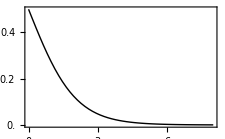

```mathematica
xTicksLst=Table[ii,{ii,0,8}];
yTicksLst=Table[jj,{jj,0,0.5,0.1}];
xPad=0.001;
figSpnAvg=Plot[Exp[-ca]/(1+Exp[-ca]),{ca,0,8},PlotRange->Full,ImageSize->8cm,Frame->True,BaseStyle->texStyle,PlotRangePadding->{None,{0,Automatic}},FrameLabel->xyLabsCAspin,FrameTicks->{{yTicksLst,None},{xTicksLst,None}},PlotStyle->styleLst]
```

```mathematica
Export[figDirStr<>"loopsMC_spnAvg.pdf",figSpnAvg]
```

figs/loopsMC_spnAvg.pdf

### Probability

```mathematica
xyLabsCAProb=matexLstFunc[{"c_A","P \\left( s_i \\right)"},labMag];
```

```mathematica
legLstCAProb=matexLstFunc[ToString/@{0,1},labMag,"prefix"->"s_i="]
```

{-Graphics-,-Graphics-}

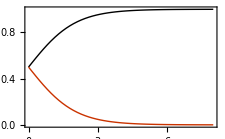

```mathematica
yRange={0,1};
figSpnProb=Plot[{1/(1+Exp[-ca]),Exp[-ca]/(1+Exp[-ca])},{ca,0,8},PlotRange->{Full,yRange},Frame->True,ImageSize->8cm,PlotRangePadding->None,BaseStyle->texStyle,FrameLabel->xyLabsCAProb,PlotLegends->Placed[LineLegend[legLstCAProb],{0.8,0.5}],PlotStyle->styleLst]
```

```mathematica
Export[figDirStr<>"loopsMC_spnProb.pdf",figSpnProb]
```

figs/loopsMC_spnProb.pdf

### zak phase plot

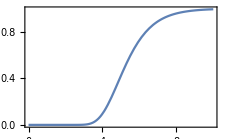

```mathematica
grdLn=64;
Plot[Table[((1-Exp[-ca])/(1+Exp[-ca]))^grdLn,{grdLn,64,64}],{ca,0,10},ImageSize->8cm,Frame->True,BaseStyle->texStyle,PlotRange->Full,PlotRangePadding->{None,Automatic}]
```

```mathematica
Log[64]//N
```

4.15888

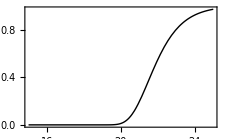

```mathematica
Plot[((1-Exp[-ca])/(1+Exp[-ca]))^(2^30),{ca,15,25},ImageSize->8cm,Frame->True,BaseStyle->texStyle,PlotRange->Full,PlotRangePadding->{None,Automatic},PlotStyle->styleLst]
```

```mathematica
Log[16]//N
```

2.77259

```mathematica
grdLnLst=Table[2^exp2,{exp2,4,9}];
```

```mathematica
legLstCAZak=matexLstFunc[ToString/@grdLnLst,labMag];
```

```mathematica
legLab=MaTeX["L=\\quad\\quad",Magnification->labMag];
```

```mathematica
xyLabCAZak=matexLstFunc[{"c_A","\\langle \\gamma \\rangle"},labMag];
```

General::munfl: 0.000306382^128 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000306382^256 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000306382^512 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

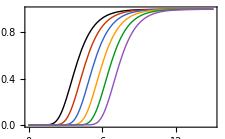

```mathematica
figZakLst=Plot[Evaluate[((1-Exp[-ca])/(1+Exp[-ca]))^grdLnLst],{ca,0,15},ImageSize->8cm,Frame->True,FrameLabel->xyLabCAZak,BaseStyle->texStyle,PlotRange->Full,PlotRangePadding->{None,Automatic},PlotStyle->styleLst,GridLines->{Log[grdLnLst/2],{Exp[-4]}},PlotLegends->Placed[LineLegend[legLstCAZak,Spacings->0.05,LegendLabel->legLab],{0.85,0.45}]]
```

```mathematica
Export[figDirStr<>"loopsMC_zak.pdf",figZakLst]
```

figs/loopsMC_zak.pdf

```mathematica
Table[{{Log[grdLnLst⟦ii⟧],colorLst⟦ii⟧},None},{ii,1,Length[grdLnLst]}]
```

{{{Log[16],GrayLevel[0]},None},{{Log[32],RGBColor[0.790588, 0.201176, 0.]},None},{{Log[48],RGBColor[0.192157, 0.388235, 0.807843]},None},{{Log[64],RGBColor[1., 0.607843, 0.]},None},{{Log[80],RGBColor[0., 0.596078, 0.109804]},None},{{Log[96],RGBColor[0.567426, 0.32317, 0.729831]},None},{{Log[112],RGBColor[0., 0.588235, 0.705882]},None},{{Log[128],RGBColor[0.8505, 0.4275, 0.13185]},None}}

## MC loops

```mathematica
divNum=64;
itNum=10000;
cArea=10;
cPerim=0;
beta = 1;
```

```mathematica
fMain="loops_MC";
fMainZakSample=fMain<>"_zakSamples";
attrLst={"divNum","itNum", "cArea", "cPerim","beta"};
fModSmart="smart";
fMod="";
```

#### Varying perimeter law

```mathematica
cPerimLst
```

{0.5,1.,1.5,2.,2.5,3.}

```mathematica
cPerimLst=Table[cP,{cP,0.5,3,0.5}];
lnCPerim=Length[cPerimLst];
cAreaLst={0.5,1.0,1.5};
lnCArea=Length[cAreaLst];
numBfieldLstLstPerim=ConstantArray[0,lnCPerim];
numLinkLstLstPerim=ConstantArray[0,lnCPerim];
zakAvgLstLstPerim=ConstantArray[0,lnCPerim];
zakSampleLstLstPerim=ConstantArray[0,lnCPerim];
```

```mathematica
numBfieldLstLstPerimSmart=ConstantArray[0,{lnCArea,lnCPerim}];
numLinkLstLstPerimSmart=ConstantArray[0,{lnCArea,lnCPerim}];
zakAvgLstLstPerimSmart=ConstantArray[0,{lnCArea,lnCPerim}];
zakSampleLstLstPerimSmart=ConstantArray[0,{lnCArea,lnCPerim}];
```

```mathematica
For[iCp=1,iCp<=lnCPerim,iCp++,
cPerim=cPerimLst⟦iCp⟧;
valLst={divNum,itNum,NumberForm[cArea,{∞,1}],If[cPerim==0,cPerim,NumberForm[cPerim,{∞,1}]],beta};
fName=fNameFun[fMain,attrLst,valLst,fMod,jld2Type];
numBfieldLstLstPerim⟦iCp⟧=readJuliaVarSqDim[fName,"numBfieldLst"];
numLinkLstLstPerim⟦iCp⟧=readJuliaVarSqDim[fName,"numLinkLst"];
zakAvgLstLstPerim⟦iCp⟧=readJuliaVarSqDim[fName,"zakMeanLst"];
zakSampleLstLstPerim⟦iCp⟧=readJuliaVarSqDim[fName,"zakLstSampleLst"];
]
```

```mathematica
For[iCa=1,iCa<=lnCArea,iCa++,
cArea=cAreaLst⟦iCa⟧;
For[iCp=1,iCp<=lnCPerim,iCp++,
cPerim=cPerimLst⟦iCp⟧;
valLst={divNum,itNum,NumberForm[cArea,{∞,1}],If[cPerim==0,cPerim,NumberForm[cPerim,{∞,1}]],beta};
fName=fNameFun[fMain,attrLst,valLst,fModSmart,jld2Type];
numBfieldLstLstPerimSmart⟦iCa,iCp⟧=readJuliaVarSqDim[fName,"numBfieldLst"];
numLinkLstLstPerimSmart⟦iCa,iCp⟧=readJuliaVarSqDim[fName,"numLinkLst"];
zakAvgLstLstPerimSmart⟦iCa,iCp⟧=readJuliaVarSqDim[fName,"zakMeanLst"];
zakSampleLstLstPerimSmart⟦iCa,iCp⟧=readJuliaVarSqDim[fName,"zakLstSampleLst"];
]
]
```

```mathematica
zakSampleLstLstPerimSmart//Dimensions
```

{3,6,100,3,64,64}

```mathematica
zakAvgLstLstPerimSmart//Dimensions
```

{3,6,10000,3}

```mathematica
zakAvgAvgLstPerimSmart=Map[Mean,zakAvgLstLstPerimSmart⟦All,All,8000;;-1,All⟧,{2}];
```

```mathematica
zakAvgAvgLstPerimSmart//Dimensions
```

{3,6,3}

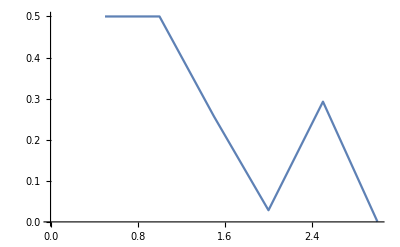

```mathematica
ListLinePlot[{cPerimLst,zakAvgAvgLstPerimSmart⟦1,All,1⟧}ᵀ]
```

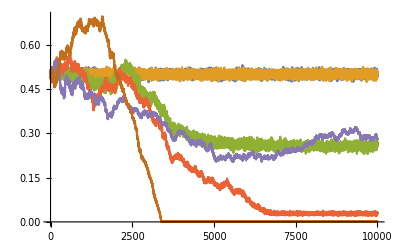

```mathematica
ListLinePlot[zakAvgLstLstPerimSmart⟦1,All,All,1⟧]
```

```mathematica
numBfieldLstLstPerimSmart//Dimensions
```

{3,6,3,10000}

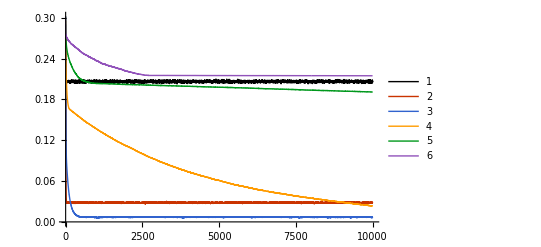

```mathematica
ListLinePlot[numBfieldLstLstPerimSmart⟦2,All,1⟧/divNum^3,PlotRange->All,PlotLegends->Automatic,PlotStyle->styleLst]
```

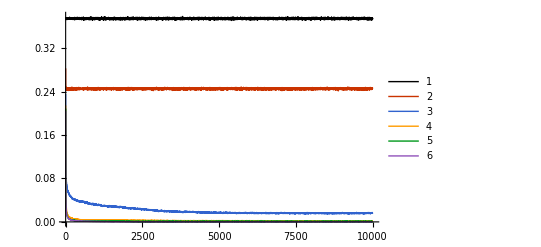

```mathematica
ListLinePlot[numLinkLstLstPerimSmart⟦1,All,1⟧/divNum^3,PlotRange->All,PlotLegends->Automatic,PlotStyle->styleLst]
```

```mathematica
numBfieldAvgLstPerimSmart=Map[Mean,numBfieldLstLstPerimSmart⟦All,All,All,8000;;-1⟧,{3}];
```

```mathematica
numLinkAvgLstPerimSmart=Map[Mean,numLinkLstLstPerimSmart⟦All,All,All,8000;;-1⟧,{3}];
```

```mathematica
numBfieldAvgLstPerimSmart//Dimensions
```

{3,6,3}

```mathematica
numLinkAvgLstPerimSmart//Dimensions
```

{3,6,3}

```mathematica
labMag
```

1.

```mathematica
xyLabsFace=matexLstFunc[{"c_L","\\langle s_{\\square} \\rangle"},labMag];
xyLabsLink=matexLstFunc[{"c_L","\\langle s_{\\mathrm{link}} \\rangle"},labMag];
```

```mathematica
xyLabsZakAvg=matexLstFunc[{"c_L","\\langle \\gamma \\rangle"},labMag];
```

```mathematica
iCa=3;
pltLab1=MaTeX["c_A = "<>ToString[cAreaLst⟦iCa⟧],Magnification->titleMag];
```

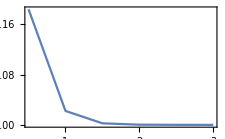

```mathematica
ListLinePlot[{cPerimLst,numLinkAvgLstPerimSmart⟦iCa,All,1⟧/64^3}ᵀ,PlotRange->All,Frame->True,BaseStyle->texStyle,PlotRangePadding->None,FrameLabel->xyLabsLink,ImageSize->8cm,PlotLabel->pltLab1]
```

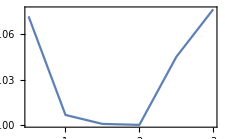

```mathematica
ListLinePlot[{cPerimLst,numBfieldAvgLstPerimSmart⟦iCa,All,1⟧/64^3}ᵀ,PlotRange->All,Frame->True,BaseStyle->texStyle,PlotRangePadding->None,FrameLabel->xyLabsFace,ImageSize->8cm,PlotLabel->pltLab1]
```

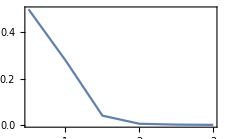

```mathematica
ListLinePlot[{cPerimLst,zakAvgAvgLstPerimSmart⟦iCa,All,1⟧}ᵀ,PlotRange->All,Frame->True,BaseStyle->texStyle,PlotRangePadding->None,FrameLabel->xyLabsZakAvg,ImageSize->8cm,PlotLabel->pltLab1]
```

```mathematica
Mean[{{1,2},{3,4}}]
```

{2,3}

```mathematica
zakSampleLstLstPerimSmartNumPN=2*zakSampleLstLstPerimSmartNum-1;
```

```mathematica
zakSampleLstLstPerimSmartNumPN⟦1,1,1,1,1⟧
```

{-1,-1,1,1,-1,1,-1,1,1,-1,1,1,1,-1,1,-1,1,-1,-1,-1,-1,-1,-1,1,-1,1,1,-1,-1,-1,-1,-1,1,1,1,-1,1,1,-1,1,-1,1,1,-1,1,-1,1,-1,1,1,-1,1,-1,1,1,1,1,1,1,1,-1,1,-1,1}

```mathematica
zakSampleLstLstPerimSmart=ConstantArray[0,Dimensions[zakSampleLstLstPerimSmartNumPN]];
```

```mathematica
zakSampleLstLstPerimSmart//Dimensions
```

{3,6,100,3,64,64}

```mathematica
zakCorrAvgLst=readJuliaVarSqDim["loops_MC_zakCorr_divNum_64_itNum_10000_cArea_0.5_cPerim_0.5_beta_1.jld2","zakCorrAvgLst"];
```

```mathematica
zakCorrAvgLst//Dimensions
```

{3,64,64}

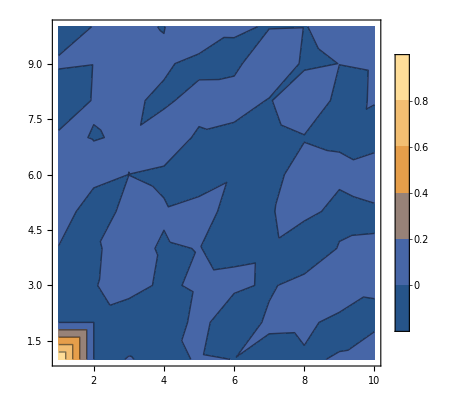

```mathematica
ListContourPlot[zakCorrAvgLst⟦1,1;;10,1;;10⟧,PlotRange->All,PlotLegends->Automatic]
```

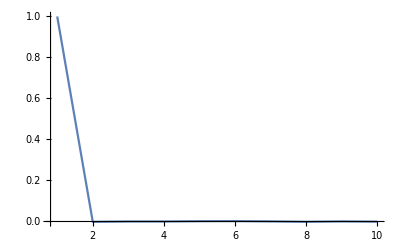

```mathematica
ListLinePlot[zakCorrAvgLst⟦1,1;;10,1⟧,PlotRange->All]
```

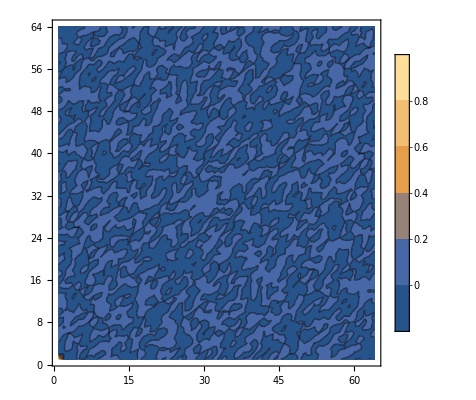

```mathematica
ListContourPlot[zakCorrAvgLst⟦1⟧,PlotRange->All,PlotLegends->Automatic]
```

```mathematica
zakSampleLstLstPerimSmartNum=zakSampleLstLstPerimSmart/.subBoolInt;
```

```mathematica
zakAvgLstLstPerimSmart=Map[Mean,zakSampleLstLstPerimSmartNum,{4,5}];
```

```mathematica
zakAvgLstLstPerimSmart//Dimensions
```

{3,6,100,3}

```mathematica
itLst=Table[it,{it,100,itNum,100}];
```

```mathematica
itLst//Dimensions
```

{100}

```mathematica
zakAvgLstLstPerimSmart[[1,1,All,1]]//Dimensions
```

{100}

```mathematica
dataLst=Table[{itLst,zakAvgLstLstPerimSmart[[iCa,iCp,All,1]]}ᵀ,{iCa,1,lnCArea},{iCp,1,lnCPerim}];
```

```mathematica
dataLst//Dimensions
```

{3,6,100,2}

```mathematica
dataLst⟦3,All⟧//Dimensions
```

{6,100,2}

```mathematica
xyLabsZakAvg=matexLstFunc[{"\\mathrm{steps}","\\langle \\gamma \\rangle"},labMag];
```

```mathematica
xyLabsZakAvg
```

matexLstFunc[{\mathrm{steps},\langle \gamma \rangle},1.]

```mathematica
matexLstFunc[{"\\mathrm{steps}","\\langle \\gamma \\rangle"},1.]
```

{-Graphics-,-Graphics-}

```mathematica
pltLab1=MaTeX["c_A = "<>ToString[cAreaLst⟦1⟧],Magnification->titleMag];
```

```mathematica
pltLab1
```

-Graphics-

```mathematica
legLstCPerim=matexLstFunc[ToString/@cPerimLst,labMag];
```

```mathematica
legLabCPerim=MaTeX["c_L=\\qquad",Magnification->labMag];
```

```mathematica
legLabCPerim
```

-Graphics-

```mathematica
legLstCPerim
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

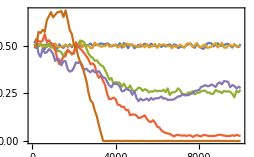

```mathematica
ListLinePlot[dataLst⟦1,All⟧,BaseStyle->texStyle,Frame->True,PlotRangePadding->None,ImageSize->9cm,FrameLabel->xyLabsZakAvg,PlotLabel->pltLab1,PlotLegends->Placed[LineLegend[legLstCPerim,Spacings->0.1,LegendLabel->legLabCPerim],Scaled[{1.1,0.5}]],PlotRangeClipping->False,ImagePadding->{{Automatic,80},{Automatic,Automatic}}]
```

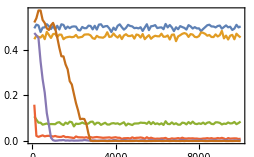

```mathematica
iCa=2;
pltLab1=MaTeX["c_A = "<>ToString[cAreaLst⟦iCa⟧],Magnification->titleMag];
ListLinePlot[dataLst⟦iCa,All⟧,BaseStyle->texStyle,Frame->True,PlotRangePadding->None,ImageSize->9cm,FrameLabel->xyLabsZakAvg,PlotLabel->pltLab1,PlotLegends->Placed[LineLegend[legLstCPerim,Spacings->0.1,LegendLabel->legLabCPerim],Scaled[{1.1,0.5}]],PlotRangeClipping->False,ImagePadding->{{Automatic,80},{Automatic,Automatic}}]
```

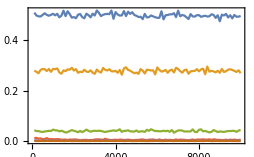

```mathematica
iCa=3;
pltLab1=MaTeX["c_A = "<>ToString[cAreaLst⟦iCa⟧],Magnification->titleMag];
ListLinePlot[dataLst⟦iCa,All⟧,BaseStyle->texStyle,Frame->True,PlotRangePadding->None,ImageSize->9cm,FrameLabel->xyLabsZakAvg,PlotLabel->pltLab1,PlotLegends->Placed[LineLegend[legLstCPerim,Spacings->0.1,LegendLabel->legLabCPerim],Scaled[{1.1,0.5}]],PlotRangeClipping->False,ImagePadding->{{Automatic,80},{Automatic,Automatic}}]
```

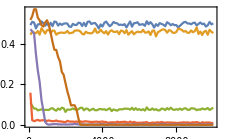

```mathematica
ListLinePlot[dataLst⟦2,All⟧,BaseStyle->texStyle,Frame->True,PlotRangePadding->None,ImageSize->8cm]
```

```mathematica
fName
```

loops_MC_divNum_64_itNum_10000_cArea_1.5_cPerim_3.0_beta_1_smart.jld2

```mathematica
zakAvgLstLstPerimSmart=ConstantArray[0,{lnCArea,lnCPerim}];
```

```mathematica
For[iCa=1,iCa<=lnCArea,iCa++,
For[iCp=1,iCp<=lnCPerim,iCp++,
zakAvgLstLstPerimSmart=
]
]
```

```mathematica
zakSampleLstLstPerimSmart//Dimensions
```

{3,6,100,3,64,64}

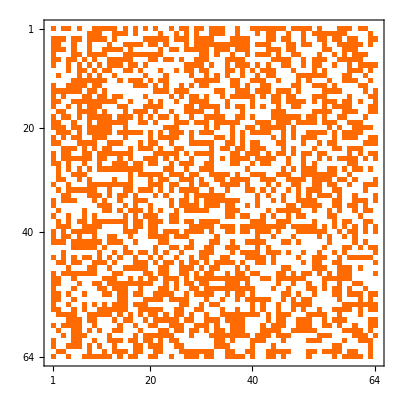

```mathematica
MatrixPlot[zakSampleLstLstPerimSmart⟦1,1,-1,1⟧/.subBoolInt]
```

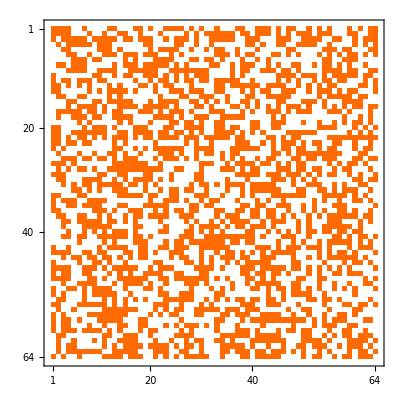

```mathematica
MatrixPlot[zakSampleLstLstPerimSmart⟦1,-1,1⟧/.subBoolInt]
```

```mathematica
cArea
```

1.5

```mathematica
mSolLst=Table[FindRoot[Tanh[-cArea/2-4cPerimLst⟦ii⟧ m^3]==-m,{m,0}],{ii,1,Length[cPerimLst]}];
```

```mathematica
mLst=m/.mSolLst
```

{0.990938,0.99985,0.999997,1.,1.,1.}

```mathematica
(1-mLst)/2
```

{0.00453117,0.0000751165,1.37109×10^-6,2.51101×10^-8,4.59906×10^-10,8.42348×10^-12}

```mathematica
(1-Tanh[cArea/2])/2
```

0.182426

```mathematica
FindRoot[Tanh[ 1.5m]-m==0,{m,1}]
```

{m→0.85856}

```mathematica
Tanh[0.5 2]
```

0.761594

```mathematica
FindRoot[Tanh[0.75-0.5 m^3]==m,{m,0}]
```

{m→0.574992}

```mathematica
NSolve[x^5-2 x+3==0,x]
```

{{x→-1.42361},{x→-0.246729-1.32082 ⅈ},{x→-0.246729+1.32082 ⅈ},{x→0.958532-0.498428 ⅈ},{x→0.958532+0.498428 ⅈ}}

```mathematica
NSolve[Tanh[0.75-0.5 m^3]==m,{m}]
```

NSolve[Tanh[0.75-0.5 m^3]==m,m]

```mathematica
numLinkLstLstPerim//Dimensions
```

{6,3,30000}

```mathematica
numLinkLinkPerim0=Append[numLinkLstLstPerim⟦All,3,All⟧,numLinkLstLst⟦4,1,All⟧];
```

```mathematica
numLinkLinkPerim0//Dimensions
```

{7,30000}

```mathematica
divNum=64;
```

```mathematica
xyLabsCL=matexLstFunc[{"\\mathrm{step}","\\langle \\mathrm{link} \\rangle"},labMag];
```

```mathematica
labMag
```

1.

```mathematica
matexLstFunc
```

matexLstFunc

```mathematica
xyLabsCL
```

{-Graphics-,-Graphics-}

```mathematica
numLinkLstLstPerim//Dimensions
```

{6,3,10000}

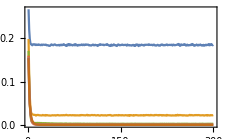

```mathematica
figPerimEvoSmart=ListLinePlot[numLinkLstLstPerimSmart⟦All,1,1;;300⟧/divNum^3,BaseStyle->texStyle,Frame->True,ImageSize->8cm,PlotRangePadding->None,FrameLabel->xyLabsCL,PlotRange->Full]
```

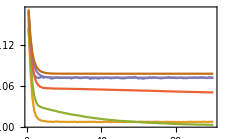

```mathematica
ListLinePlot[numBfieldLstLstPerimSmart⟦All,1,1;;100⟧/divNum^3,BaseStyle->texStyle,Frame->True,ImageSize->8cm,PlotRangePadding->None,FrameLabel->xyLabsCL,PlotRange->Full]
```

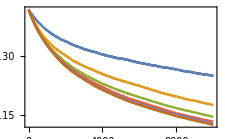

```mathematica
figPerimEvo=ListLinePlot[numLinkLstLstPerim⟦All,1,All⟧/divNum^3,BaseStyle->texStyle,Frame->True,ImageSize->8cm,PlotRangePadding->None,FrameLabel->xyLabsCL]
```

```mathematica
figPerimEvo=ListLinePlot[numLinkLstLstPerim⟦All,1,All⟧/divNum^3,BaseStyle->texStyle,Frame->True,ImageSize->8cm,PlotRangePadding->None,FrameLabel->xyLabsCL]
```

-Graphics-

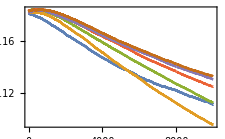

```mathematica
ListLinePlot[numBfieldLstLstPerim⟦All,1,All⟧/divNum^3,BaseStyle->texStyle,Frame->True,ImageSize->8cm,PlotRangePadding->None,FrameLabel->xyLabsCL]
```

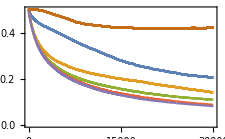

```mathematica
figPerimEvo=ListLinePlot[numLinkLinkPerim0⟦{1,3,4,5,6,7},All⟧/divNum^3,BaseStyle->texStyle,Frame->True,ImageSize->8cm,PlotRangePadding->None,FrameLabel->xyLabsCL]
```

```mathematica
Export[figDirStr<>"loopsMC_perimEvo.pdf",figPerimEvo]
```

figs/loopsMC_perimEvo.pdf

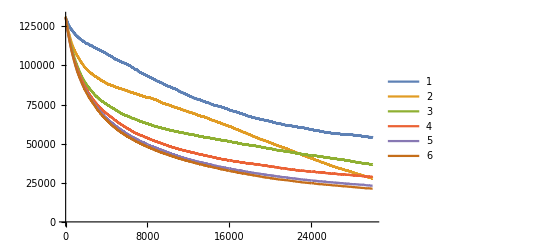

```mathematica
ListLinePlot[numLinkLstLstPerim⟦All,1,All⟧,PlotLegends->Automatic]
```

```mathematica
zakSampleLstLstNumPerim=zakSampleLstLstPerim/.subBoolInt;
```

```mathematica
"c_A="<>ToString[cArea]<>", c_L="
```

c_A=1.5, c_L=

```mathematica
"c_A=1.5, c_L="
```

```mathematica
cpLstLab=matexLstFunc[ToString/@cPerimLst,labMag,"prefix"->"c_A="<>ToString[cArea]<>",\, c_L="];
```

```mathematica
cpLstLab
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cpcaLab=MaTeX["c_A="<>ToString[cArea]<>",\, c_L="<>ToString[cPerim]]
```

-Graphics-

```mathematica
zakSampleLstLstPerimSmart//Dimensions
```

{3,6,100,3,64,64}

```mathematica
cPerimLst
```

{0.5,1.,1.5,2.,2.5,3.}

```mathematica
it
```

101

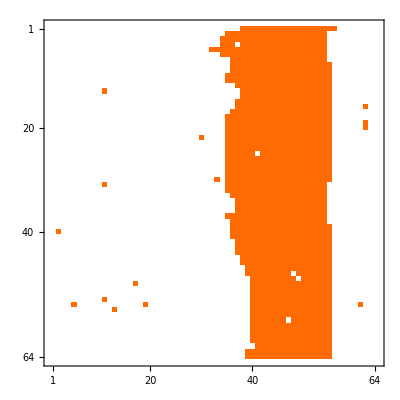

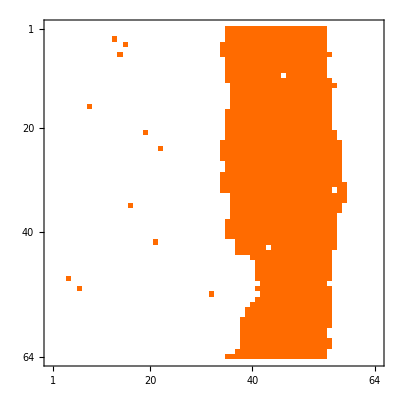

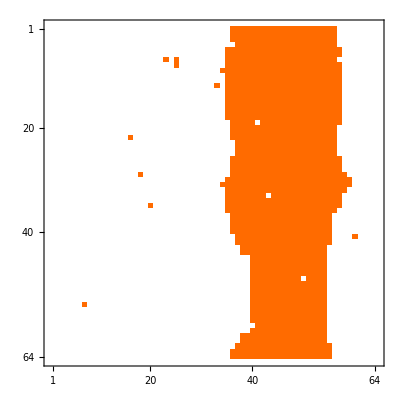

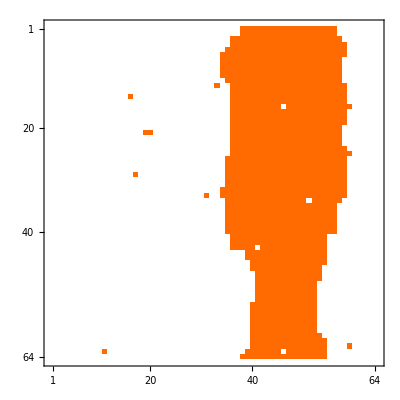

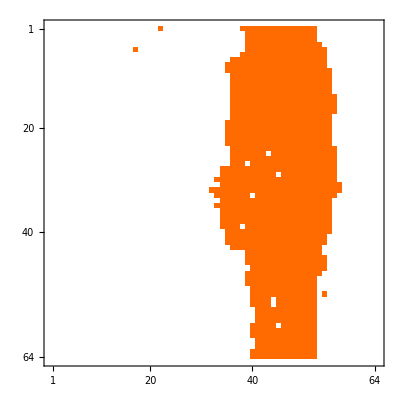

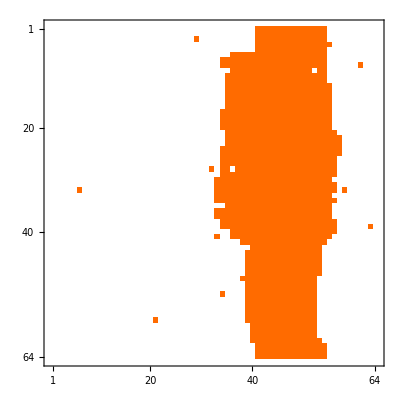

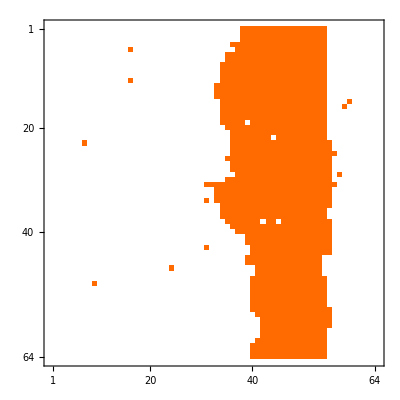

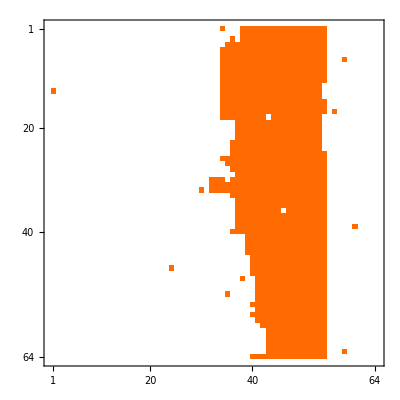

```mathematica
For[it=91,it<=100,it++,
Print[MatrixPlot[zakSampleLstLstPerimSmart⟦1,5,it,1⟧/.subBoolInt]];
]
```

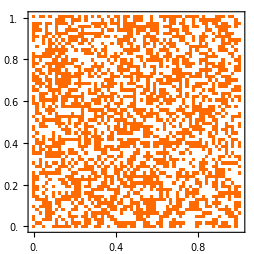

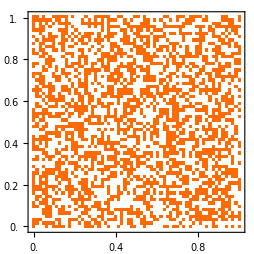

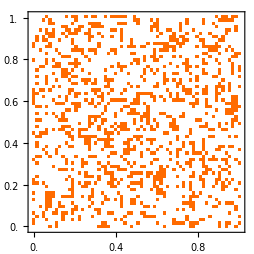

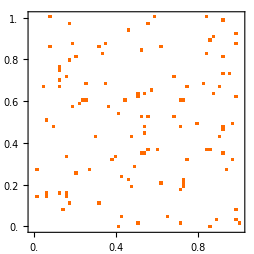

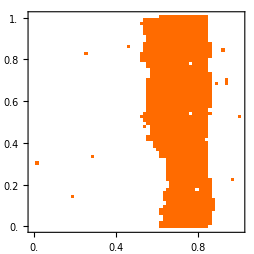

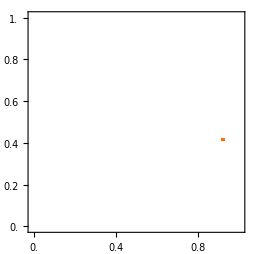

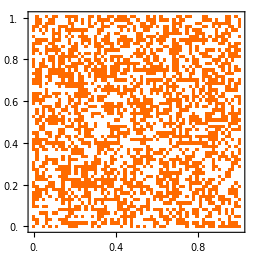

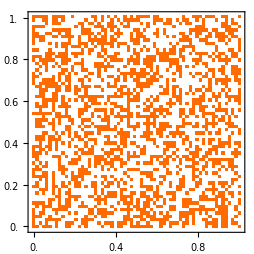

-Graphics-

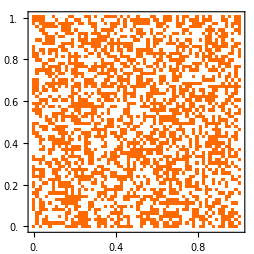

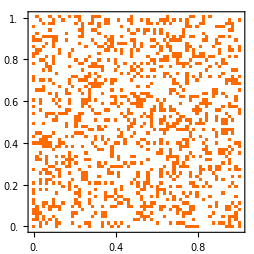

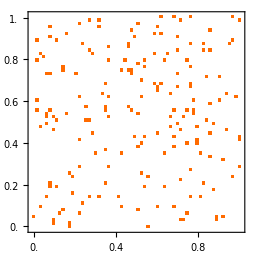

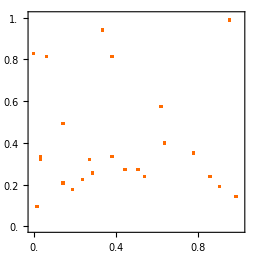

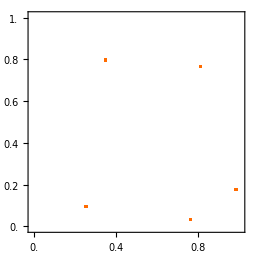

-Graphics-

```mathematica
For[iCa=1,iCa<=lnCArea,iCa++,
cArea=cAreaLst⟦iCa⟧;
For[iCp=1,iCp<=lnCPerim,iCp++,
cPerim=cPerimLst⟦iCp⟧;
cpcaLab=MaTeX["c_A="<>ToString[cArea]<>",\, c_L="<>ToString[cPerim]];
plotThis=MatrixPlot[zakSampleLstLstPerimSmart⟦iCa,iCp,-1,1⟧/.subBoolInt,PlotRangePadding->None,BaseStyle->texStyle,DataRange->{{0,1},{0,1}},DataReversed->False,FrameTicks->{{zakXTicks,False},{zakYTicks,False}},FrameLabel->xyLabsZak,PlotLabel->cpcaLab,ImageSize->9cm];
Print[plotThis];
Export[figDirStr<>"zakLast_cPerim_"<>ToString[NumberForm[cPerimLst⟦iCp⟧,{∞,1}]]<>"_cArea_"<>ToString[cArea]<>".pdf",plotThis];
]
]
```

#### No perimeter law

```mathematica
cAreaLst=Table[ca,{ca,0.5,8,0.5}];
lnCArea=Length[cAreaLst];
cPerim=0;
```

```mathematica
numBfieldLstLst=ConstantArray[0,lnCArea];
numLinkLstLst=ConstantArray[0,lnCArea];
zakAvgLstLst=ConstantArray[0,lnCArea];
```

```mathematica
zakSampleLstLst=ConstantArray[0,lnCArea];
```

```mathematica
fName
```

loops_MC_divNum_64_itNum_30000_cArea_8._cPerim_0_beta_1.jld2

```mathematica
For[iCa=1,iCa<=lnCArea,iCa++,
cArea=cAreaLst⟦iCa⟧;
valLst={divNum,itNum,NumberForm[cArea,{∞,1}],NumberForm[cPerim,{∞,1}],beta};
fName=fNameFun[fMain,attrLst,valLst,fMod,jld2Type];
fNameZakSample=fNameFun[fMainZakSample,attrLst,valLst,fMod,jld2Type];
numBfieldLstLst⟦iCa⟧=readJuliaVarSqDim[fName,"numBfieldLst"];
numLinkLstLst⟦iCa⟧=readJuliaVarSqDim[fName,"numLinkLst"];
zakAvgLstLst⟦iCa⟧=readJuliaVarSqDim[fName,"zakMeanLst"];
zakSampleLstLst⟦iCa⟧=readJuliaVarSqDim[fName,"zakLstSampleLst"];
]
```

```mathematica
numLinkLstLst//Dimensions
```

{17,3,30000}

```mathematica
cAreaLst
```

{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.}

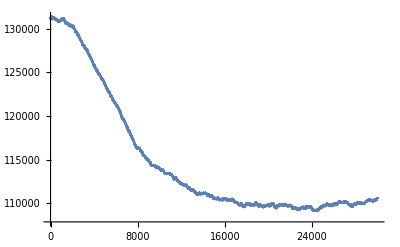

```mathematica
ListLinePlot[numLinkLstLst⟦4,1,All⟧]
```

```mathematica
ListLinePlot[numLinkLstLst⟦1;;8,1,All⟧]
```

-Graphics-

```mathematica
ListLinePlot[numLinkLstLst⟦All,1,All⟧]
```

-Graphics-

```mathematica
zakSampleLstLstNum=zakSampleLstLst/.subBoolInt;
```

```mathematica
zakXTicks=Table[ii,{ii,0,1,0.2}];
zakYTicks=Table[ii,{ii,0,1,0.2}];
```

```mathematica
xyLabsZak=matexLstFunc[{"\\theta_1","\\theta_2"},labMag];
```

```mathematica
caLstLab=matexLstFunc[ToString/@(NumberForm[#,{∞,1}]&/@cAreaLst),labMag,"prefix"->"c_A="];
```

```mathematica
caLab=MaTeX["c_A",Magnification->labMag];
```

```mathematica
Log[divNum/4]//N
```

2.77259

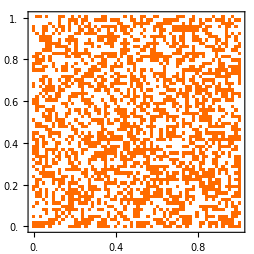

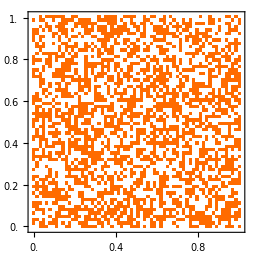

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

```mathematica
For[iCa=1,iCa<=lnCArea,iCa++,
plotThis=MatrixPlot[zakSampleLstLstNum⟦iCa,-1,1⟧,PlotRangePadding->None,DataRange->{{0,1},{0,1}},DataReversed->False,FrameTicks->{{zakXTicks,False},{zakYTicks,False}},FrameLabel->xyLabsZak,PlotLabel->caLstLab⟦iCa⟧,ImageSize->9cm];
Print[plotThis];
Export[figDirStr<>"zakLast_cArea_"<>ToString[NumberForm[cAreaLst⟦iCa⟧,{∞,1}]]<>".pdf",plotThis];
]
```

```mathematica
MatrixPlot[zakSampleLstLstNum⟦2,-1,1⟧]
```

-Graphics-

```mathematica
zakSampleLstLstNum//Dimensions
```

{17,100,3,64,64}

```mathematica
numBfieldLstLst//Dimensions
```

{17,3,30000}

```mathematica
64^3
```

262144

```mathematica
legLstMCSavg
```

{0.0, 0.5, 1.0, 1.5, 2.0, 2.5, 3.0, 3.5, 4.0, 4.5, 5.0, 5.5, 6.0, 6.5, 7.0, 7.5, 8.0}

```mathematica
cAreaLstFormatted=NumberForm[#,{∞,1}]&/@cAreaLst;
```

```mathematica
cAreaLstFormatted⟦1⟧
```

0.0

```mathematica
ToString/@Evaluate[NumberForm[cAreaLst,{∞,1}]]
```

NumberForm::iprf: Formatting specification {Infinity, 1} should be a positive integer or a pair of positive integers.

{0., 0.5, 1., 1.5, 2., 2.5, 3., 3.5, 4., 4.5, 5., 5.5, 6., 6.5, 7., 7.5, 8.}

```mathematica
NumberForm[cAreaLst,{∞,1}]
```

{0.0,0.5,1.0,1.5,2.0,2.5,3.0,3.5,4.0,4.5,5.0,5.5,6.0,6.5,7.0,7.5,8.0}

```mathematica
xyLabsMCSavg
```

matexLstFunc[{\mathrm{step},\langle s \rangle}]

```mathematica
xyLabsMCSavg=matexLstFunc[{"\\mathrm{step}","\\langle s \\rangle"},labMag];
```

```mathematica
legLstMCSavg=matexLstFunc[ToString/@(NumberForm[#,{∞,1}]&/@cAreaLst),labMag];
```

```mathematica
legLabMCSavg=MaTeX["c_A = \\quad",Magnification->labMag];
```

```mathematica
idCut=8;
figSpnAvgMC=ListLinePlot[numBfieldLstLst⟦1;;idCut,1,All⟧/divNum^3,BaseStyle->texStyle,Frame->True,FrameLabel->xyLabsMCSavg,PlotStyle->styleLst,ImageSize->10cm,PlotLegends->Placed[LineLegend[legLstMCSavg⟦1;;idCut⟧,Spacings->0.1,LegendLabel->legLabMCSavg],{1,0.6}]]
```

-Graphics-

```mathematica
Export[figDirStr<>"loopsMC_spnAvg_MCevo.pdf",figSpnAvgMC]
```

figs/loopsMC_spnAvg_MCevo.pdf

```mathematica
sAvgLst=Map[Mean,numBfieldLstLst⟦All,All,20000;;-1⟧,{2}];
```

```mathematica
sAvgLst//Dimensions
```

{17,3}

```mathematica
zakAvgLstLst//Dimensions
```

{17,30000,3}

```mathematica
xyLabsMCZak=matexLstFunc[{"\\mathrm{step}","\\gamma"},labMag];
```

```mathematica
xyLabsMCZak=matexLstFunc[{"\\mathrm{step}","\\gamma"},labMag];
```

```mathematica
xyLabsMCZak
```

matexLstFunc[{\mathrm{step},\gamma},1.]

```mathematica
idCut=8;
figZakAvgMCevo=ListLinePlot[1-2zakAvgLstLst⟦All,All,1⟧,BaseStyle->texStyle,Frame->True,FrameLabel->xyLabsMCZak,PlotStyle->styleLst,ImageSize->8cm,PlotRange->Full]
```

-Graphics-

```mathematica
Export[figDirStr<>"loopsMC_zakAvgEvo.pdf",figZakAvgMCevo]
```

figs/loopsMC_zakAvgEvo.pdf

```mathematica
sAvgLstData={cAreaLst,sAvgLst⟦All,1⟧/divNum^3}ᵀ;
```

```mathematica
sAvgLstData//Dimensions
```

{17,2}

```mathematica
zakAvgAvgLst=1-2Map[Mean,zakAvgLstLst⟦All,25000;;-1,1⟧,{1}];
```

```mathematica
zakAvgAvgLst//Dimensions
```

{17}

```mathematica
zakAvgAvgDat={cAreaLst,zakAvgAvgLst}ᵀ;
```

```mathematica
figZakAvgAvgDat=Show[figZakLst,ListPlot[zakAvgAvgDat]]
```

-Graphics-

```mathematica
Export[figDirStr<>"loopsMC_zakAvgDat.pdf",figZakAvgAvgDat]
```

figs/loopsMC_zakAvgDat.pdf

```mathematica
figSpnAvgDat=Show[figSpnAvg,ListPlot[sAvgLstData,PlotRange->All,PlotStyle->styleLst⟦2;;-1⟧]]
```

-Graphics-

```mathematica
Export[figDirStr<>"loopsMC_spnAvgDat.pdf",figSpnAvgDat]
```

figs/loopsMC_spnAvgDat.pdf

```mathematica
legLstMCSavg⟦1⟧
```

Part::partd: Part specification {0.0, 0.5, 1.0, 1.5, 2.0, 2.5, 3.0, 3.5, 4.0, 4.5, 5.0, 5.5, 6.0, 6.5, 7.0, 7.5, 8.0}⟦1⟧ is longer than depth of object.

{0.0, 0.5, 1.0, 1.5, 2.0, 2.5, 3.0, 3.5, 4.0, 4.5, 5.0, 5.5, 6.0, 6.5, 7.0, 7.5, 8.0}⟦1⟧

```mathematica
legLstMCSavg
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[numBfieldLstLst⟦{1,-1},1,All⟧/divNum^3,BaseStyle->texStyle,Frame->True,FrameLabel->xyLabsMCSavg,PlotStyle->styleLst,ImageSize->10cm,PlotLegends->Placed[LineLegend[legLstMCSavg⟦{1,-1}⟧,Spacings->Small,LegendLabel->legLabMCSavg],{1,0.8}]]
```

-Graphics-

```mathematica
NumerForm[itNum,{∞,1}]
```

NumerForm[100,{∞,1}]

```mathematica
fMain="loops_MC";
fMainZakMean=fMain<>"_"<>"zakMeanLst";
attrLst={"divNum","itNum", "cArea", "cPerim","beta"};
valLst={divNum,itNum,cArea,NumberForm[cPerim,{∞,1}],NumberForm[beta,{∞,1}]};
fMod="";
```

```mathematica
fName=fNameFun[fMain,attrLst,valLst,fMod,jld2Type];
fNameZakMean=fNameFun[fMainZakMean,attrLst,valLst,fMod,jld2Type];
```

```mathematica
fName
```

loops_MC_divNum_64_itNum_30000_cArea_10_cPerim_0_beta_1.jld2

```mathematica
fNameZakMean
```

loops_MC_zakMeanLst_divNum_64_itNum_10000_cArea_3_cPerim_0_beta_1.jld2

```mathematica
"loops_MC_zakMeanLst_divNum_64_itNum_10000_cArea_1.0_cPerim_0.0_beta_1.0.jld2"
```

```mathematica
"loops_MC_divNum_128.0_itNum_100.0_cArea_0.1_cPerim_50.0_beta_1.jld2"
```

loops_MC_divNum_128.0_itNum_100.0_cArea_0.1_cPerim_50.0_beta_1.0.jld2

```mathematica
fName="loops_MC_divNum_64.0_itNum_10000.0_cArea_3.0_cPerim_0.0_beta_1.0.jld2";
```

```mathematica
fNameZakMean="loops_MC_zakMeanLst_divNum_64_itNum_10000_cArea_3.0_cPerim_0.0_beta_1.jld2";
```

```mathematica
zakLstLst=readJuliaVarSqDim[fName,"zakLstLst"];
```

```mathematica
numBfieldLst=readJuliaVarSqDim[fName,"numBfieldLst"];
```

```mathematica
numLinkLst=readJuliaVarSqDim[fName,"numLinkLst"];
```

```mathematica
zakMeanLst=readJuliaVarSqDim[fName,"zakMeanLst"];
```

```mathematica
zakMeanLst=readJuliaVarSqDim[fNameZakMean,"zakMeanLst"];
```

```mathematica
zakMeanLst//Dimensions
```

{1000,3}

```mathematica
ListLinePlot[numBfieldLst⟦1⟧]
```

-Graphics-

```mathematica
fNameTest="loops_MC_zakSamples_divNum_16_itNum_1000_cArea_4_cPerim_0_beta_1.jld2";
```

```mathematica
zakSampleLst=readJuliaVarSqDim[fNameTest,"zakLstSampleLst"];
```

```mathematica
zakSampleLst//Dimensions
```

{100,3,16,16}

```mathematica
MatrixPlot[zakSampleLst⟦100,1⟧/.subBoolInt]
```

-Graphics-

```mathematica
ListLinePlot[zakMeanLst⟦All,1⟧,PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[numBfieldLst⟦1⟧]
```

-Graphics-

```mathematica
ListLinePlot[zakMeanLst⟦All,1⟧,PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[zakMeanLst⟦All,1⟧,PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[zakMeanLst⟦All,1⟧,PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[zakMeanLst⟦All,3⟧]
```

-Graphics-

```mathematica
numBfieldLst⟦1⟧
```

1044117

```mathematica
ListLinePlot[numLinkLst⟦1⟧]
```

-Graphics-

```mathematica
E//N
```

2.71828

```mathematica
(1/E)/(1+1/E)//N
```

0.268941

```mathematica
16^3  (1/E)/(1+1/E)//N
```

1101.58

```mathematica
64^3
```

262144

```mathematica
(1/E)/(1+1/E)//N
```

0.268941

```mathematica
E^-3//N
```

0.0497871

```mathematica
129460 /64^3//N
```

0.493851

```mathematica
131000-129000
```

2000

```mathematica
64^2
```

4096

```mathematica
16^3 (1/E)/(1+1/E)//N
```

1101.58

```mathematica
ListLinePlot[numBfieldLst⟦1⟧,PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[numBfieldLst⟦1,1;;1000⟧,PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[numBfieldLst⟦1,100;;500⟧,PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[numBfieldLst⟦3,1;;10000⟧,PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[numLinkLst⟦1⟧]
```

-Graphics-

```mathematica
ListLinePlot[numBfieldLst⟦1⟧]
```

-Graphics-

```mathematica
ListLinePlot[numBfieldLst⟦1⟧]
```

-Graphics-

```mathematica
ListLinePlot[numBfieldLst⟦1⟧]
```

-Graphics-

```mathematica
ListLinePlot[numBfieldLst⟦1⟧]
```

-Graphics-

```mathematica
ListLinePlot[numBfieldLst⟦3,201;;300⟧]
```

-Graphics-

```mathematica
128^3
```

2097152

```mathematica
Plot[Exp[-b]/(1+Exp[-b]),{b,0,10},PlotRange->All]
```

-Graphics-

```mathematica
zakLstLstPerim5Area1=zakLstLst;
```

```mathematica
zakLstLstNum=zakLstLst/.{True->1,False->0};
```

$Aborted

```mathematica
Total[zakLstLst⟦100,2⟧/.{True->1,False->0}]
```

{55,63,68,58,63,54,64,62,67,67,67,64,64,61,55,67,63,62,64,71,65,56,62,59,62,58,56,66,63,74,55,54,70,65,61,59,67,65,69,60,62,56,61,64,61,67,54,55,59,61,67,58,72,59,65,59,61,62,65,68,67,73,64,62,66,71,67,64,58,71,61,54,72,58,65,58,62,71,60,72,64,64,71,71,56,58,61,65,63,63,67,68,69,67,60,67,75,57,65,62,66,58,64,63,60,65,50,69,71,66,52,68,80,67,58,58,68,67,67,69,59,58,63,65,72,71,64,68}

```mathematica
Total[zakLstLst⟦100,1⟧/.{True->1,False->0}]
```

{65,67,66,61,67,63,64,57,76,55,68,69,62,54,62,54,63,65,60,65,69,63,58,66,58,67,65,61,70,64,75,68,62,65,55,69,69,60,63,52,67,55,58,65,64,64,56,60,63,74,64,77,68,64,64,67,66,64,63,64,59,63,53,61,66,68,65,64,57,65,67,66,65,65,63,66,73,67,71,64,74,75,62,63,62,69,61,59,63,55,60,65,62,61,62,59,60,70,58,58,69,74,65,58,63,61,67,61,71,57,53,64,70,74,62,72,65,67,64,69,62,58,70,60,64,65,66,72}

```mathematica
zakLstLst//Dimensions
```

{1000,3,16,16}

```mathematica
numZakLstTest=Total[zakLstLst/.subBoolInt,{3,4}];
```

```mathematica
numZakLstTest//Dimensions
```

{1000,3}

```mathematica
ListLinePlot[numZakLstTest⟦All,1⟧]
```

-Graphics-

```mathematica
numZakLst=;
```

```mathematica
plotThis=MatrixPlot[zakLstLst⟦1000,1⟧/.{True->1,False->0},PlotRangePadding->None,DataRange->{{0,1},{0,1}},DataReversed->False,FrameTicks->{{Automatic,False},{Automatic,False}},ImageSize->9cm]
```

-Graphics-

```mathematica
plotPerim50Beta1It100
```

-Graphics-

```mathematica
plotPerim50Beta1
```

-Graphics-

```mathematica
plotPerimArea50Beta10
```

-Graphics-

```mathematica
plotPerim5Area1=plotThis;
```

```mathematica
plotPerim5Area1
```

-Graphics-

```mathematica
plotBeta10=MatrixPlot[zakLstLstBeta10⟦900,1⟧/.{True->1,False->0},PlotRangePadding->None,DataRange->{{0,1},{0,1}},DataReversed->False,FrameTicks->{{Automatic,False},{Automatic,False}},ImageSize->9cm]
```

-Graphics-

```mathematica
plotBeta1=MatrixPlot[zakLstLstBeta1⟦10,3⟧/.{True->1,False->0},PlotRangePadding->None,DataRange->{{0,1},{0,1}},DataReversed->False,FrameTicks->{{Automatic,False},{Automatic,False}},ImageSize->9cm]
```

-Graphics-

```mathematica
zakLstLstNum64=zakLstLstNum;
```

```mathematica
MatrixPlot[zakLstLstNum64⟦100,3⟧]
```

-Graphics-

```mathematica
MatrixPlot[zakLstLst⟦1,3⟧/.{True->1,False->0}]
```

-Graphics-

```mathematica
fName="loops_MC_divNum_64_itNum_10000_cArea_1.0_cPerim_2.0_beta_1.jld2";
```

```mathematica
linkSampleLst=readJuliaVarSqDim[fName,"linkSampleLst"];
```

```mathematica
BfieldSampleLst=readJuliaVarSqDim[fName,"BfieldSampleLst"];
```

```mathematica
BfieldSampleLst//Dimensions
```

{100,3,4,4,4}

```mathematica
linkSampleLst//Dimensions
```

{100,3,64,64,64}

```mathematica
lineLst={};
```

```mathematica
divNum=64;
divStep=1/divNum;
nDim=3;
coord=ConstantArray[0,nDim];
```

```mathematica
linkSampleLst//Dimensions
```

{100,3,64,64,64}

```mathematica
linkDimLst={{2,3},{1,3},{1,2}};
```

```mathematica
faceLst={};
it=1;
For[ix=1,ix<=divNum,ix++,
For[iy=1,iy<=divNum,iy++,
For[iz=1,iz<=divNum,iz++,
For[iD=1,iD<=3,iD++,
If[BfieldSampleLst⟦it,iD⟧⟦ix,iy,iz⟧,
coord⟦1⟧=ix-1;coord⟦2⟧=iy-1;
coord⟦3⟧=iz-1;
coord=coord divStep;
coord2=coord;
coord2⟦linkDimLst⟦iD,1⟧⟧+=divStep;
(*coord2=Mod[coord2,1];*)
coord3=coord;
coord3⟦linkDimLst⟦iD,2⟧⟧+=divStep;
(*coord3=Mod[coord3,1];*)
coord4=coord2;
coord4⟦linkDimLst⟦iD,2⟧⟧=coord3⟦linkDimLst⟦iD,2⟧⟧;
AppendTo[faceLst,Polygon[{coord,coord2,coord4,coord3}]];
]
]
]
]
]
```

```mathematica
linkLstTest=ConstantArray[False,{nDim,divNum,divNum,divNum}];
```

```mathematica
linkDimLst
```

{{2,3},{1,3},{1,2}}

```mathematica
!True
```

False

```mathematica
f[#]&@@{1,2,3}
```

f[1]

```mathematica
FullForm[{1,1,1}]
```

List[1,1,1]

```mathematica
linkSampleLst//Dimensions
```

{100,3,64,64,64}

```mathematica
fun=linkSampleLst⟦1,1,##⟧&
```

linkSampleLst⟦1,1,##1⟧&

```mathematica
fun[1,1,1]
```

True

```mathematica
linkSampleLst⟦1,1,1,2,3⟧
```

False

```mathematica
linkSampleLst⟦1,1,##⟧&@@{1,2,3}
```

False

```mathematica
divNum
```

4

```mathematica
nDim
```

3

```mathematica
linkLstTest=ConstantArray[False,{nDim,divNum,divNum,divNum}];
For[ix=1,ix<=divNum,ix++,
For[iy=1,iy<=divNum,iy++,
For[iz=1,iz<=divNum,iz++,
For[iD=1,iD<=nDim,iD++,
If[BfieldSampleLst⟦it,iD⟧⟦ix,iy,iz⟧,
For[id2=1,id2<=2,id2++,
dim2=linkDimLst⟦iD,id2⟧;
linkLstTest⟦dim2,ix,iy,iz⟧=!linkLstTest⟦dim2,ix,iy,iz⟧;
For[id3=1,id3<=2,id3++,
dim3=linkDimLst⟦iD,id3⟧;
If[dim3!=dim2,
coord={ix,iy,iz};
coord⟦dim3⟧+=1;
coord⟦dim3⟧=Mod[coord⟦dim3⟧-1,divNum]+1;
ix2=coord⟦1⟧;iy2=coord⟦2⟧;iz2=coord⟦3⟧;
linkLstTest⟦dim2,ix2,iy2,iz2⟧=!linkLstTest⟦dim2,ix2,iy2,iz2⟧;
]
]
]
]
]
]
]
]
```

```mathematica
linkLstTest=linkSampleLst⟦-1⟧;
```

```mathematica
linkLstTest//Dimensions
```

{3,64,64,64}

```mathematica
linkLstTest⟦dim2,##⟧&@@coord=False
```

Set::write: Tag Apply in (linkLstTest⟦dim2,##1⟧&)@@{1,4,4} is Protected.

False

```mathematica
area=5;
gamma=0.01;
```

```mathematica
Plot[{Log[(3 2^nExp)/area-1],2ArcTanh[gamma^(1/2^nExp)]},{nExp,1,5},PlotRange->All]
```

-Graphics-

```mathematica
True=False
```

Set::wrsym: Symbol True is Protected.

False

```mathematica
faceLst//Dimensions
```

{83}

```mathematica
coord2
```

{0,1/4,3/4}

```mathematica
coord3
```

{0,0,0}

```mathematica
coord4
```

{0,1/4,0}

```mathematica
coord
```

{1,1,3/4}

```mathematica
Graphics3D[faceLst]
```

-Graphics3D-

```mathematica
lineTestLst//Dimensions
```

{112107}

```mathematica
linkLstTest//Dimensions
```

{3,64,64,64}

```mathematica
lineTestLst={};
it=-1;
For[ix=1,ix<=divNum,ix++,
For[iy=1,iy<=divNum,iy++,
For[iz=1,iz<=divNum,iz++,
For[iD=1,iD<=3,iD++,
If[linkLstTest⟦iD,ix,iy,iz⟧,
coord⟦1⟧=ix-1;coord⟦2⟧=iy-1;
coord⟦3⟧=iz-1;
coord=coord divStep;
coordSh=coord;
coordSh⟦iD⟧+=divStep;
(*coordSh⟦iD⟧=Mod[coordSh⟦iD⟧,1];*)
AppendTo[lineTestLst,Line[{coord,coordSh}]];
]
]
]
]
]
```

$Aborted

```mathematica
lineTestLst//Dimensions
```

{18404}

```mathematica
lineLst={};
it=-1;
For[ix=1,ix<=divNum,ix++,
For[iy=1,iy<=divNum,iy++,
For[iz=1,iz<=divNum,iz++,
For[iD=1,iD<=3,iD++,
If[linkSampleLst⟦it,iD⟧⟦ix,iy,iz⟧,
coord⟦1⟧=ix-1;coord⟦2⟧=iy-1;
coord⟦3⟧=iz-1;
coord=coord divStep;
coordSh=coord;
coordSh⟦iD⟧+=divStep;
(*coordSh⟦iD⟧=Mod[coordSh⟦iD⟧,1];*)
AppendTo[lineLst,Line[{coord,coordSh}]];
]
]
]
]
]
```

$Aborted

```mathematica
lineLst//Dimensions
```

{9623}

```mathematica
Mod[1.3,1]
```

0.3

```mathematica
linkSampleLst⟦it,3⟧⟦2,1,1⟧
```

True

```mathematica
iD=1
```

1

```mathematica
coord⟦1⟧=ix;coord⟦2⟧=iy;
coord⟦3⟧=iz;
coord=coord divStep;
coordSh=coord;
coordSh⟦iD⟧+=divStep;
Append[lineLst,Line[{coord,coordSh}]];
```

Part::partw: Part 4 of {5/4,5/4,5/4} does not exist.

Set::partw: Part 4 of {5/4,5/4,5/4} does not exist.

```mathematica
lineLst//Dimensions
```

{48}

```mathematica
Total[linkSampleLst⟦10,3⟧/.subBoolInt,All]
```

22

```mathematica
Graphics3D[lineLst]
```

-Graphics3D-

```mathematica
Graphics3D[lineTestLst]
```

-Graphics3D-

```mathematica
figLoopLines=Graphics3D[lineLst]
```

-Graphics3D-

```mathematica
Export[figDirStr<>"loopsMC_loopLines.pdf",figLoopLines]
```

figs/loopsMC_loopLines.pdf

-Graphics3D-

```mathematica
Graphics3D[lineLst]
```

-Graphics3D-

```mathematica
lineLst//Dimensions
```

{0}

```mathematica
lineLst
```

{}

```mathematica
coord
```

{1,1,1/16}

```mathematica
coordSh
```

{17/16,1,1/16}

```mathematica
lineLst⟦1,1,1⟧
```

Line[{{0.,0.,0.},{0.,0.,0.1}}]

```mathematica
lineLst=Table[Line[{{a,b,c},{a,b,c+0.1}}],{a,0,1,0.25},{b,0,1,0.25},{c,0,1,0.25}];
```

```mathematica
lineLst⟦1,1,1⟧
```

Line[{{0.,0.,0.},{0.,0.,0.1}}]

```mathematica
Graphics3D[lineLst]
```

-Graphics3D-

```mathematica
fName="loops_MC_divNum_64_itNum_10000_cArea_1.0_cPerim_1.0_beta_1_smart.jld2";
```

```mathematica
numBfieldLst=readJuliaVarSqDim[fName,"numBfieldLst"];
```

```mathematica
numBfieldLst//Dimensions
```

{3,10000}

```mathematica
64^3/2
```

131072

```mathematica
Exp[-3]/(1+Exp[-3])//N
```

0.0474259

```mathematica
ListLinePlot[numBfieldLst2⟦1⟧/64^3]
```

-Graphics-

```mathematica
ListLinePlot[numBfieldLst2⟦1⟧]
```

-Graphics-

```mathematica
64^3
```

262144

```mathematica
ListLinePlot[numBfieldLst⟦1⟧/64^3]
```

-Graphics-

```mathematica
ListLinePlot[numBfieldLst⟦1⟧/64^3]
```

-Graphics-

## Zak plots

### Params

```mathematica
divNum=64;
cAreaLst=Table[cA,{cA,0.5,1.5,0.5}];
numCArea=Length[cAreaLst];
cPerimLst=Table[cP,{cP,-0.5,-3,-0.5}];
numCPerim=Length[cPerimLst];
beta=1;
itNum=10000;
fMod="smart";
```

```mathematica
fMain="loops_MC";
fMainZakSample=fMain<>"_"<>"zakLstSampleMean";
attrLst={"divNum","itNum","cArea","cPerim","beta"};
```

### Storage

```mathematica
zakLstSampleLst=ConstantArray[0,{numCArea,numCPerim}];
```

```mathematica
For[iCa=1,iCa<=numCArea,iCa++,
cArea=valDecForm[cAreaLst⟦iCa⟧,1];
For[iCp=1,iCp<=numCPerim,iCp++,
cPerim=valDecForm[cPerimLst⟦iCp⟧,1];
valLst={divNum,itNum,cArea,cPerim,beta};
fName=fNameFun[fMainZakSample,attrLst,valLst,fMod,jld2Type];
zakLstSampleLst⟦iCa,iCp⟧=readJuliaVarSqDim[fName,"zakLstSampleLst"];
]]
```

```mathematica
cPerimLst
```

{-0.5,-1.,-1.5,-2.,-2.5,-3.}

```mathematica
cPerimLst⟦5⟧
```

-2.5

```mathematica
zakLstSampleLstNum=zakLstSampleLst/.subBoolInt;
```

```mathematica
zakLstSampleLstNum//Dimensions
```

{3,6,100,3,64,64}

```mathematica
cPerimLst
```

{-0.5,-1.,-1.5,-2.,-2.5,-3.}

```mathematica
MatrixPlot[zakLstSampleLstNum⟦1,5,50,1⟧]
```

-Graphics-

```mathematica
tickLst=Table[tc,{tc,0,1,0.2}];
```

```mathematica
xyLabs=matexLstFunc[{"\\theta_1 / 2\\pi","\\theta_2 / 2\\pi"},labMag];
```

```mathematica
xyLabs
```

{-Graphics-,-Graphics-}

```mathematica
pltLabLst=Table[MaTeX["c_A="<>ToString[cAreaLst⟦iCa⟧]<>", c_L="<>ToString[cPerimLst⟦iCp⟧],Magnification->labMag],{iCa,1,numCArea},{iCp,1,numCPerim}];
```

```mathematica
For[iCa=1,iCa<=numCArea,iCa++,
cArea=cAreaLst⟦iCa⟧;
For[iCp=1,iCp<=numCPerim,iCp++,
cPerim=cPerimLst⟦iCp⟧;
Print[MatrixPlot[zakLstSampleLstNum⟦iCa,iCp,1,1⟧,PlotRangePadding->None,ImageSize->8cm,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},FrameLabel->xyLabs,DataReversed->False,BaseStyle->texStyle,PlotLabel->pltLabLst⟦iCa,iCp⟧]]
]]
```

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

```mathematica
zakLstSampleLst⟦1,1⟧//Dimensions
```

{100,3,64,64}

```mathematica
ListLinePlot[zakLstSampleLst⟦1,6,1,1,All,1⟧/.subBoolInt]
```

-Graphics-

```mathematica
zakLstSampleLst//Dimensions
```

{3,6,100,3,64,64}

```mathematica
MatrixPlot[zakLstSampleLst⟦1,4,10,1⟧/.subBoolInt]
```

-Graphics-

```mathematica
valDecForm[cAreaLst⟦2⟧,1]
```

1.0

```mathematica
NumberForm[cAreaLst⟦2⟧,{∞,1}]valDecFormvalD
```

1.0

```mathematica
cArea=valDecForm[cAreaLst⟦2⟧,1];
cPerim=valDecForm[cPerimLst⟦2⟧,1];
```

```mathematica
cPerim
```

-1.0

```mathematica
valLst={divNum,itNum,cArea,cPerim,beta};
fName=fNameFun[fMainZakSample,attrLst,valLst,fMod,jld2Type];
```

```mathematica
fName
```

loops_MC_zakLstSampleMean_divNum_64_itNum_10000_cArea_1.0_cPerim_-1.0_beta_1_smart.jld2

```mathematica
valDecForm[cAreaLst⟦2⟧,1]
```

valDecForm[1.,1]

```mathematica
zakLstTest=readJuliaVarSqDim["loops_MC_divNum_64_itNum_5_cArea_0.5_cPerim_-2.5_beta_1.jld2","zakLstLst"];
```

```mathematica
zakLstTest//Dimensions
```

{5,3,64,64}

```mathematica
MatrixPlot[zakLstTest⟦5,1⟧/.subBoolInt]
```

-Graphics-

```mathematica
zakCorrLstTest=readJuliaVarSqDim["loops_MC_zakCorr_divNum_64_itNum_10000_cArea_0.5_cPerim_0.5_beta_1.jld2","zakCorrAvgLst"];
```

```mathematica
"loops_MC_zakCorrStats_divNum_64_itNum_10000_cArea_0.5_cPerim_-2.5_beta_1.jld2"
```

```mathematica
zakCorrLstTest2=readJuliaVarSqDim["loops_MC_zakCorr_divNum_64_itNum_5_cArea_0.5_cPerim_-2.5_beta_1.jld2","zakCorrLst"];
```

```mathematica
zakCorrLstTest2//Dimensions
```

{5,3,64,64}

```mathematica
ListPlot[zakCorrLstTest2⟦1,1,All,1⟧,PlotRange->All]
```

-Graphics-

```mathematica
zakCorrLstTest//Dimensions
```

{3,64,64}

```mathematica
zakCorrLstTest2//Dimensions
```

{3,64,64}

```mathematica
ListContourPlot[zakCorrLstTest2⟦1⟧,PlotRange->All]
```

-Graphics-

```mathematica
ListContourPlot[zakCorrLstTest⟦1⟧,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[zakCorrLstTest2⟦1,All,1⟧,PlotRange->All]
```

-Graphics-

```mathematica
Total[zakCorrLstTest⟦1,All,1⟧]
```

0.989714

```mathematica
ListPlot[zakCorrLstTest⟦1,All,1⟧,PlotRange->All]
```

-Graphics-

```mathematica
zakCorrSampleTest=readJuliaVarSqDim["loops_MC_zakCorrSample_divNum_64_itNum_10000_cArea_0.5_cPerim_-2.5_beta_1_smart.jld2","zakCorrSampleLst"];
```

```mathematica
zakCorrAvgTest=readJuliaVarSqDim["loops_MC_zakCorrStats_divNum_64_itNum_10000_cArea_0.5_cPerim_-2.5_beta_1_smart.jld2","zakCorrAvgLst"];
```

```mathematica
zakCorrSampleTest//Dimensions
```

{100,3,64,64}

```mathematica
ListContourPlot[zakCorrSampleTest⟦5,1,All,All⟧,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[zakCorrSampleTest⟦5,1,All,1⟧,PlotRange->All]
```

-Graphics-

```mathematica
zakCorrAvgTest//Dimensions
```

{3,64,64}

```mathematica
ListContourPlot[zakCorrAvgTest⟦1⟧,PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
ListPlot[zakCorrAvgTest⟦1,All,1⟧,PlotRange->All]
```

-Graphics-

```mathematica
cPerimLst
```

{-0.5,-1.,-1.5,-2.,-2.5,-3.}

```mathematica
fNameTest="loopsSample_divNum_64_itNum_10000_cArea_0.5_cPerim_-1.5_beta_1_smart.jld2";
```

```mathematica
numLinkLstTest=readJuliaVarSqDim[fNameTest,"numLinkLst"];
```

```mathematica
numBfieldLstTest=readJuliaVarSqDim[fNameTest,"numBfieldLst"];
```

```mathematica
linkSampleLstTest=readJuliaVarSqDim[fNameTest,"linkSampleLst"];
```

```mathematica
linkSampleLstTest//Dimensions
```

{100,3,64,64,64}

```mathematica
divStep=1/divNum;
nDim=3;
coord=ConstantArray[0,nDim];
```

```mathematica
lineLst={};
it=-1;
For[ix=1,ix<=divNum,ix++,
For[iy=1,iy<=divNum,iy++,
For[iz=1,iz<=divNum,iz++,
For[iD=1,iD<=3,iD++,
If[linkSampleLstTest⟦it,iD⟧⟦ix,iy,iz⟧,
coord⟦1⟧=ix-1;coord⟦2⟧=iy-1;
coord⟦3⟧=iz-1;
coord=coord divStep;
coordSh=coord;
coordSh⟦iD⟧+=divStep;
(*coordSh⟦iD⟧=Mod[coordSh⟦iD⟧,1];*)
AppendTo[lineLst,Line[{coord,coordSh}]];
]
]
]
]
]
```

$Aborted

```mathematica
numLinkLstTest//Dimensions
```

{3,10000}

```mathematica
ListPlot[numLinkLstTest⟦1⟧,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[numBfieldLstTest⟦1⟧]
```

-Graphics-

```mathematica
ListPlot[numLinkLstTest⟦1⟧]
```

-Graphics-

```mathematica
ListPlot[numBfieldLstTest⟦1⟧]
```

-Graphics-

```mathematica
ListPlot[numLinkLstTest⟦1⟧,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[numBfieldLstTest⟦1⟧]
```

-Graphics-

```mathematica
ListPlot[numLinkLstTest⟦1⟧,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[numBfieldLstTest⟦1⟧,PlotRange->All]
```

-Graphics-

```mathematica
numLinkLstTest⟦1,1⟧
```

200762

```mathematica
numBfieldLstTest⟦1,1⟧
```

111527

```mathematica
ListPlot[numLinkLstTest⟦1,1;;100⟧,PlotRange->All]
```

-Graphics-

```mathematica
zakLstSampleLstNum//Dimensions
```

{3,6,100,3,64,64}

### Mid/end game zak pattern

```mathematica
For[iCa=1,iCa<=numCArea,iCa++,
cArea=cAreaLst⟦iCa⟧;
For[iCp=1,iCp<=numCPerim,iCp++,
cPerim=cPerimLst⟦iCp⟧;
Print[MatrixPlot[zakLstSampleLstNum⟦iCa,iCp,50,2⟧,PlotRangePadding->None,ImageSize->8cm,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},FrameLabel->xyLabs,DataReversed->False,BaseStyle->texStyle,PlotLabel->pltLabLst⟦iCa,iCp⟧]]
]]
```

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

```mathematica
For[iCa=1,iCa<=numCArea,iCa++,
cArea=cAreaLst⟦iCa⟧;
For[iCp=1,iCp<=numCPerim,iCp++,
cPerim=cPerimLst⟦iCp⟧;
Print[MatrixPlot[zakLstSampleLstNum⟦iCa,iCp,3,1⟧,PlotRangePadding->None,ImageSize->8cm,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},FrameLabel->xyLabs,DataReversed->False,BaseStyle->texStyle,PlotLabel->pltLabLst⟦iCa,iCp⟧]]
]]
```

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

```mathematica
For[iCa=1,iCa<=numCArea,iCa++,
cArea=cAreaLst⟦iCa⟧;
For[iCp=1,iCp<=numCPerim,iCp++,
cPerim=cPerimLst⟦iCp⟧;
Print[MatrixPlot[zakLstSampleLstNum⟦iCa,iCp,100,2⟧,PlotRangePadding->None,ImageSize->8cm,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},FrameLabel->xyLabs,DataReversed->False,BaseStyle->texStyle,PlotLabel->pltLabLst⟦iCa,iCp⟧]]
]]
```

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

### Finer

```mathematica
divNum=64;
cAreaLstFine=Table[cA,{cA,0.5,0.5}];
numCAreaFine=Length[cAreaLstFine];
cPerimLstFine=Table[cP,{cP,-1.5,-2.0,-0.05}];
numCPerimFine=Length[cPerimLstFine];
beta=1;
itNum=10000;
fMod="smart";
```

```mathematica
cAreaLstFine
```

{0.5}

```mathematica
zakLstSampleLstFine=ConstantArray[0,{numCAreaFine,numCPerimFine}];
```

```mathematica
numCAreaFine
```

1

```mathematica
For[iCa=1,iCa<=numCAreaFine,iCa++,
cArea=valDecForm[cAreaLstFine⟦iCa⟧,1];
For[iCp=1,iCp<=numCPerimFine,iCp++,
cPerim=valDecForm[cPerimLstFine⟦iCp⟧,1];
valLst={divNum,itNum,cArea,cPerim,beta};
fName=fNameFun[fMainZakSample,attrLst,valLst,fMod,jld2Type];
zakLstSampleLstFine⟦iCa,iCp⟧=readJuliaVarSqDim[fName,"zakLstSampleLst"];
]]
```

```mathematica
zakLstSampleLstFine//Dimensions
```

{1,11,100,3,64,64}

```mathematica
zakLstSampleLstFineNum=zakLstSampleLstFine/.subBoolInt;
```

```mathematica
pltLabLstFine=Table[MaTeX["c_A="<>ToString[cAreaLstFine⟦iCa⟧]<>", c_L="<>ToString[cPerimLstFine⟦iCp⟧],Magnification->labMag],{iCa,1,numCAreaFine},{iCp,1,numCPerimFine}];
```

```mathematica
For[iCa=1,iCa<=numCAreaFine,iCa++,
cArea=cAreaLstFine⟦iCa⟧;
For[iCp=1,iCp<=numCPerimFine,iCp++,
cPerim=cPerimLstFine⟦iCp⟧;
Print[MatrixPlot[zakLstSampleLstFineNum⟦iCa,iCp,3,1⟧,PlotRangePadding->None,ImageSize->8cm,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},FrameLabel->xyLabs,DataReversed->False,BaseStyle->texStyle,PlotLabel->pltLabLstFine⟦iCa,iCp⟧]]
]]
```

-Graphics-

-Graphics-

-Graphics-

«8 more identical outputs»

```mathematica
linkPlotLst=readJuliaVar["linkLstForMathematica_sliced_divNum_64_itNum_10000_cArea_0.5_cPerim_-3.0_beta_1_smart.jld2","linkPlotLstSlice"];
```

```mathematica
linkPlotLst⟦1,2⟧//Dimensions
```

{262000,2,3}

```mathematica
Line[#]&/@linkPlotLst⟦1,1⟧⟦1;;10⟧
```

{Line[{{0.,0.,0.},{0.015625,0.,0.}}],Line[{{0.015625,0.,0.},{0.03125,0.,0.}}],Line[{{0.03125,0.,0.},{0.046875,0.,0.}}],Line[{{0.046875,0.,0.},{0.0625,0.,0.}}],Line[{{0.0625,0.,0.},{0.078125,0.,0.}}],Line[{{0.078125,0.,0.},{0.09375,0.,0.}}],Line[{{0.09375,0.,0.},{0.109375,0.,0.}}],Line[{{0.109375,0.,0.},{0.125,0.,0.}}],Line[{{0.125,0.,0.},{0.140625,0.,0.}}],Line[{{0.140625,0.,0.},{0.15625,0.,0.}}]}

```mathematica
Line[linkPlotLst⟦1,1⟧⟦1⟧]
```

Line[{{0.,0.,0.},{0.015625,0.,0.}}]

```mathematica
Join[linkPlotLst⟦1,1⟧⟦1;; 64^2⟧,linkPlotLst⟦2,1⟧⟦1;; 64^2⟧,1]//Dimensions
```

{8192,2,3}

```mathematica
linkPlotLst⟦3,1⟧//Dimensions
```

{261626,2,3}

```mathematica
Graphics3D[Line[#]&/@Join[linkPlotLst⟦3,1⟧⟦1;; 2 64^2⟧,1]]
```

-Graphics3D-

```mathematica
Graphics3D[Line[#]&/@Join[linkPlotLst⟦1,1⟧⟦1;; 64^2⟧,linkPlotLst⟦2,1⟧⟦1;; 64^2⟧,1]]
```

-Graphics3D-

```mathematica
Graphics3D[Line[#]&/@linkPlotLst⟦1,1⟧⟦1;; 64^2⟧~~Join~~linkPlotLst⟦2,1⟧⟦1;; 64^2⟧]
```

-Graphics3D-

```mathematica
linkLst2=readJuliaVar["linkLstForMathematica_sliced_divNum_64_itNum_10000_cArea_0.5_cPerim_0.5_beta_1_smart.jld2","linkPlotLstSlice"];
```

ExternalEvaluate::invalidSession: The session … is invalid and cannot be used.

```mathematica
linkLst2⟦1,1⟧//Dimensions
```

{}

```mathematica
Graphics3D[Line[#]&/@linkLst2⟦1,1⟧⟦1;;64^2⟧]
```

Part::take: Cannot take positions 1 through 4096 in 0.0625.

Part::pkspec1: The expression Line[1;;4096] cannot be used as a part specification.

-Graphics3D-

## Loops with centered beta

```mathematica
divNum=64;
itNum=10000;
betaMinMax={0.2,100.0};
betaBase=1;
```

```mathematica
tickLst=Table[tc,{tc,0,1,0.2}];
```

```mathematica
fNameParamLst="loops_paramLst_divNum_64_itNum_10000_beta_[0.2, 100.0]_cRatio_[0.1353352832366127, 7.38905609893065]_withInit0.jld2";
```

```mathematica
betaLst=readJuliaVarSqDim[fNameParamLst,"betaLst"];
cRatioLst=readJuliaVarSqDim[fNameParamLst,"cRatioLst"];
cAreaLst=readJuliaVarSqDim[fNameParamLst,"cAreaLst"];
cPerimLst=readJuliaVarSqDim[fNameParamLst,"cPerimLst"];
cAreaStrLst=readJuliaVarSqDim[fNameParamLst,"cAreaStrLst"];
cPerimStrLst=readJuliaVarSqDim[fNameParamLst,"cPerimStrLst"];
betaStrLst=readJuliaVarSqDim[fNameParamLst,"betaStrLst"];
```

```mathematica
betaLst
```

{0.2,0.5,1.,2.,3.,10.,100.}

```mathematica
cRatioLst
```

{0.135335,0.165299,0.201897,0.246597,0.301194,0.367879,0.449329,0.548812,0.67032,0.818731,1.,1.2214,1.49182,1.82212,2.22554,2.71828,3.32012,4.0552,4.95303,6.04965,7.38906}

```mathematica
lnBeta=Length[betaLst];
lnRatio=Length[cRatioLst];
fModBase="smart";
fModInit0=fModBase<>"_"<>"isInit0";
fModLstInit0={fModBase,fModInit0};
lnInit0=Length[fModLstInit0];
```

```mathematica
fModInit0
```

smart_isInit0

```mathematica
{lnBeta,lnRatio}
```

{7,21}

36.78797

```mathematica
NumberForm[cAreaLst⟦-1⟧,1000]
```

{36.78794411714423,40.6569659740599,44.93289641172216,49.65853037914096,54.88116360940265,60.65306597126335,67.03200460356394,74.08182206817179,81.8730753077982,90.483741803596,100.,110.5170918075648,122.140275816017,134.9858807576003,149.182469764127,164.8721270700128,182.2118800390509,201.3752707470477,222.5540928492467,245.960311115695,271.8281828459045}

```mathematica
zakLstLst=ConstantArray[0,{lnBeta,lnRatio,lnInit0}];
loopsLstLst=ConstantArray[0,{lnBeta,lnRatio,lnInit0}];
```

```mathematica
attrLst={"divNum","itNum","cArea","cPerim","beta"};
valLst={divNum,itNum,1,1,betaBase};
fMainZakLst="loops_MC_zakLstSampleMean";
fMainLoopLst="loopsSample";
```

```mathematica
cAreaLst⟦-1⟧
```

{36.7879,40.657,44.9329,49.6585,54.8812,60.6531,67.032,74.0818,81.8731,90.4837,100.,110.517,122.14,134.986,149.182,164.872,182.212,201.375,222.554,245.96,271.828}

```mathematica
For[iBeta=1,iBeta<=lnBeta,iBeta++,
For[iRatio=1,iRatio<=lnRatio,iRatio++,
For[iInit0=1,iInit0<=lnInit0,iInit0++,
cAreaStr=cAreaStrLst⟦iBeta,iRatio⟧;
cPerimStr=cPerimStrLst⟦iBeta,iRatio⟧;
(*betaStr=betaStrLst⟦iBeta⟧;*)
betaStr=betaBase;
valLst⟦3⟧=cAreaStr;
valLst⟦4⟧=cPerimStr;
valLst⟦5⟧=betaStr;
fMod=fModLstInit0⟦iInit0⟧;
fNameZakLst=fNameFun[fMainZakLst,attrLst,valLst,fMod,jld2Type];
fNameLoopLst=fNameFun[fMainLoopLst,attrLst,valLst,fMod,jld2Type];
zakLstLst⟦iBeta,iRatio,iInit0⟧=readJuliaVarSqDim[fNameZakLst,"zakLstSampleLst"];
(*loopsLstLst⟦iBeta,iRatio,iInit0⟧=readJuliaVarSqDim[fNameLoopLst,"linkSampleLst"];*)
]
]
]
```

```mathematica
valLst⟦3⟧=cAreaStrLst⟦-2,1⟧;
valLst⟦4⟧=cPerimStrLst⟦-2,1⟧;
```

```mathematica
cAreaLst⟦-2⟧
```

{3.67879,4.0657,4.49329,4.96585,5.48812,6.06531,6.7032,7.40818,8.18731,9.04837,10.,11.0517,12.214,13.4986,14.9182,16.4872,18.2212,20.1375,22.2554,24.596,27.1828}

```mathematica
loopsLstLst⟦-2,1,1⟧=readJuliaVarSqDim[fNameLoopLst,"linkSampleLst"];
```

```mathematica
loopsLstLst⟦-2,1,1⟧//Dimensions
```

{100,3,64,64,64}

```mathematica
betaLst⟦-2⟧
```

10.

```mathematica
fMod=fModLstInit0⟦1⟧;
```

```mathematica
valLst
```

{64,10000,3.6787944117144233,-27.18281828459045,1}

```mathematica
zakLstLst//Dimensions
```

{7,21,2}

```mathematica
zakLstLst⟦-1,1,1⟧//Dimensions
```

{100,3,64,64}

```mathematica
fNameLoopLst=fNameFun[fMainLoopLst,attrLst,valLst,fMod,jld2Type];
```

```mathematica
iRatio
```

22

```mathematica
zakLstLst⟦-1,1,1,1,1⟧//Dimensions
```

{64,64}

```mathematica
zakLstLst⟦-1,1,1,1,1⟧//Dimensions
```

{100,3,64,64}

```mathematica
MatrixPlot[zakLstLst⟦1,1,1,1,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
betaLst
```

{0.2,0.5,1.,2.,3.,10.,100.}

```mathematica
MatrixPlot[zakLstLst⟦-2,2,1,1,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
MatrixPlot[zakLstLst⟦1,1,1,100,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm]
```

-Graphics-

```mathematica
MatrixPlot[zakLstLst⟦4,1,2,10,1⟧/.subBoolInt]
```

-Graphics-

```mathematica
cAreaLst⟦-2⟧
```

{3.67879,4.0657,4.49329,4.96585,5.48812,6.06531,6.7032,7.40818,8.18731,9.04837,10.,11.0517,12.214,13.4986,14.9182,16.4872,18.2212,20.1375,22.2554,24.596,27.1828}

```mathematica
cPerimLst⟦-2⟧
```

{-27.1828,-24.596,-22.2554,-20.1375,-18.2212,-16.4872,-14.9182,-13.4986,-12.214,-11.0517,-10.,-9.04837,-8.18731,-7.40818,-6.7032,-6.06531,-5.48812,-4.96585,-4.49329,-4.0657,-3.67879}

```mathematica
Exp[1]//N
```

2.71828

```mathematica
cRatioLst
```

{0.135335,0.165299,0.201897,0.246597,0.301194,0.367879,0.449329,0.548812,0.67032,0.818731,1.,1.2214,1.49182,1.82212,2.22554,2.71828,3.32012,4.0552,4.95303,6.04965,7.38906}

## Loops with centered beta

```mathematica
divNum=64;
itNum=30000;
betaMinMax={5,15};
betaBase=1;
```

```mathematica
tickLst=Table[tc,{tc,0,1,0.2}];
```

```mathematica
fNameParamLst="loops_paramLst_divNum_64_itNum_30000_beta_[5, 15]_cRatio_[0.049787068367863944, 0.36787944117144233]_withInit0.jld2";
```

```mathematica
betaLst=readJuliaVarSqDim[fNameParamLst,"betaLst"];
cRatioLst=readJuliaVarSqDim[fNameParamLst,"cRatioLst"];
cAreaLst=readJuliaVarSqDim[fNameParamLst,"cAreaLst"];
cPerimLst=readJuliaVarSqDim[fNameParamLst,"cPerimLst"];
cAreaStrLst=readJuliaVarSqDim[fNameParamLst,"cAreaStrLst"];
cPerimStrLst=readJuliaVarSqDim[fNameParamLst,"cPerimStrLst"];
betaStrLst=readJuliaVarSqDim[fNameParamLst,"betaStrLst"];
```

```mathematica
cRatioLst
```

{0.0497871,0.0550232,0.0608101,0.0672055,0.0742736,0.082085,0.090718,0.100259,0.110803,0.122456,0.135335,0.149569,0.165299,0.182684,0.201897,0.22313,0.246597,0.272532,0.301194,0.332871,0.367879}

```mathematica
cPerimStrLst⟦1⟧
```

{-22.40844535169032,-21.315572575844087,-20.275999834223374,-19.287127653484873,-18.34648333809622,-17.451714787309207,-16.600584613682734,-15.790964548448839,-15.020830119732166,-14.28825559031582,-13.591409142295225,-12.92854829657923,-12.29801555578475,-11.698234259629954,-11.127704642462339,-10.585000083063374,-10.068763537352382,-9.57770414506948,-9.110594001952544,-8.666265089336976,-8.24360635350064}

```mathematica
betaLst
```

{5,6,7,8,9,10,11,12,13,14,15}

```mathematica
cRatioLst
```

{0.0497871,0.0550232,0.0608101,0.0672055,0.0742736,0.082085,0.090718,0.100259,0.110803,0.122456,0.135335,0.149569,0.165299,0.182684,0.201897,0.22313,0.246597,0.272532,0.301194,0.332871,0.367879}

```mathematica
lnBeta=Length[betaLst];
lnRatio=Length[cRatioLst];
fModBase="smart";
fModInit0=fModBase<>"_"<>"isInit0";
fModLstInit0={fModBase,fModInit0};
lnInit0=Length[fModLstInit0];
```

```mathematica
fModInit0
```

smart_isInit0

```mathematica
{lnBeta,lnRatio}
```

{7,21}

36.78797

```mathematica
NumberForm[cAreaLst⟦-1⟧,1000]
```

{36.78794411714423,40.6569659740599,44.93289641172216,49.65853037914096,54.88116360940265,60.65306597126335,67.03200460356394,74.08182206817179,81.8730753077982,90.483741803596,100.,110.5170918075648,122.140275816017,134.9858807576003,149.182469764127,164.8721270700128,182.2118800390509,201.3752707470477,222.5540928492467,245.960311115695,271.8281828459045}

```mathematica
zakLstLst=ConstantArray[0,{lnBeta,lnRatio,lnInit0}];
loopsLstLst=ConstantArray[0,{lnBeta,lnRatio,lnInit0}];
```

```mathematica
attrLst={"divNum","itNum","cArea","cPerim","beta"};
valLst={divNum,itNum,1,1,betaBase};
fMainZakLst="loops_MC_zakLstSampleMean";
fMainLoopLst="loopsSample";
```

```mathematica
cAreaLst⟦-1⟧
```

{36.7879,40.657,44.9329,49.6585,54.8812,60.6531,67.032,74.0818,81.8731,90.4837,100.,110.517,122.14,134.986,149.182,164.872,182.212,201.375,222.554,245.96,271.828}

```mathematica
lnBeta
```

11

```mathematica
cAreaStrLst⟦6⟧
```

{2.2313016014842986,2.3457028809379765,2.465969639416065,2.592402606458915,2.725317930340126,2.865047968601901,3.0119421191220215,3.1663676937905323,3.3287108369807954,3.499377491111553,3.6787944117144233,3.8674102345450123,4.065696597405991,4.274149319487267,4.493289641172216,4.723665527410147,4.965853037914095,5.22045776761016,5.488116360940265,5.7694981038048665,6.065306597126334}

```mathematica
cPerimStrLst⟦6⟧
```

{-44.81689070338064,-42.63114515168817,-40.55199966844675,-38.57425530696975,-36.69296667619244,-34.903429574618414,-33.20116922736547,-31.581929096897678,-30.04166023946433,-28.57651118063164,-27.18281828459045,-25.85709659315846,-24.5960311115695,-23.39646851925991,-22.255409284924678,-21.170000166126748,-20.137527074704764,-19.15540829013896,-18.221188003905088,-17.332530178673952,-16.48721270700128}

```mathematica
zakLstLst⟦1,1,1⟧//Dimensions
```

{100,3,64,64}

```mathematica
fNameZakLst
```

loops_MC_zakLstSampleMean_divNum_64_itNum_30000_cArea_2.814843457125572_cPerim_-51.15737418202581_beta_1_smart_isInit0.jld2

```mathematica
cAreaStrLst⟦7⟧
```

{2.4544317616327285,2.5802731690317744,2.712566603357671,2.8516428671048066,2.9978497233741384,3.151552765462091,3.3131363310342237,3.4830044631695856,3.661581920678875,3.8493152402227087,4.046673852885865,4.2541512579995135,4.4722662571465905,4.701564251435994,4.942618605289438,5.196032080151162,5.4624383417055045,5.742503544371177,6.036927997034292,6.346447914185353,6.671837256838968}

```mathematica
zakLstLstTmpInit0=readJuliaVarSqDim["loops_MC_zakLstSampleMean_divNum_64_itNum_30000_cArea_2.4544317616327285_cPerim_-49.29857977371871_beta_1_smart_isInit0.jld2","zakLstSampleLst"];
```

```mathematica
zakLstLstTmp=readJuliaVarSqDim["loops_MC_zakLstSampleMean_divNum_64_itNum_30000_cArea_2.4544317616327285_cPerim_-49.29857977371871_beta_1_smart.jld2","zakLstSampleLst"];
```

```mathematica
zakLstLstTmp//Dimensions
```

{100,3,64,64}

```mathematica
For[iBeta=1,iBeta<=lnBeta,iBeta++,
For[iRatio=1,iRatio<=lnRatio,iRatio++,
For[iInit0=1,iInit0<=lnInit0,iInit0++,
cAreaStr=cAreaStrLst⟦iBeta,iRatio⟧;
cPerimStr=cPerimStrLst⟦iBeta,iRatio⟧;
(*betaStr=betaStrLst⟦iBeta⟧;*)
betaStr=betaBase;
valLst⟦3⟧=cAreaStr;
valLst⟦4⟧=cPerimStr;
valLst⟦5⟧=betaStr;
fMod=fModLstInit0⟦iInit0⟧;
fNameZakLst=fNameFun[fMainZakLst,attrLst,valLst,fMod,jld2Type];
fNameLoopLst=fNameFun[fMainLoopLst,attrLst,valLst,fMod,jld2Type];
zakLstLst⟦iBeta,iRatio,iInit0⟧=readJuliaVarSqDim[fNameZakLst,"zakLstSampleLst"];
(*loopsLstLst⟦iBeta,iRatio,iInit0⟧=readJuliaVarSqDim[fNameLoopLst,"linkSampleLst"];*)
]
]
]
```

ArrayReshape::listrp: List or SparseArray or structured array expected at position 1 in ….

General::stop: Further output of ArrayReshape::listrp will be suppressed during this calculation.

ExternalEvaluate::invalidSession: The session … is invalid and cannot be used.

General::stop: Further output of ExternalEvaluate::invalidSession will be suppressed during this calculation.

$Aborted

```mathematica
valLst⟦3⟧=cAreaStrLst⟦-2,1⟧;
valLst⟦4⟧=cPerimStrLst⟦-2,1⟧;
```

```mathematica
cAreaLst⟦-2⟧
```

{3.67879,4.0657,4.49329,4.96585,5.48812,6.06531,6.7032,7.40818,8.18731,9.04837,10.,11.0517,12.214,13.4986,14.9182,16.4872,18.2212,20.1375,22.2554,24.596,27.1828}

```mathematica
loopsLstLst⟦-2,1,1⟧=readJuliaVarSqDim[fNameLoopLst,"linkSampleLst"];
```

```mathematica
loopsLstLst⟦-2,1,1⟧//Dimensions
```

{100,3,64,64,64}

```mathematica
betaLst⟦-2⟧
```

10.

```mathematica
Log[cRatioLst]
```

{-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.}

```mathematica
fMod=fModLstInit0⟦1⟧;
```

```mathematica
valLst
```

{64,10000,3.6787944117144233,-27.18281828459045,1}

```mathematica
zakLstLst//Dimensions
```

{7,21,2}

```mathematica
zakLstLst⟦-1,1,1⟧//Dimensions
```

{100,3,64,64}

```mathematica
fNameLoopLst=fNameFun[fMainLoopLst,attrLst,valLst,fMod,jld2Type];
```

```mathematica
iRatio
```

22

```mathematica
zakLstLst⟦-1,1,1,1,1⟧//Dimensions
```

{64,64}

```mathematica
zakLstLst⟦-1,1,1,1,1⟧//Dimensions
```

{100,3,64,64}

```mathematica
betaLst
```

{5,6,7,8,9,10,11,12,13,14,15}

```mathematica
zakLstLst⟦6,1,1⟧//Dimensions
```

{2}

```mathematica
MatrixPlot[zakLstLst⟦6,1,1,1,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

Part::partw: Part 100 of ArrayReshape[$Failed,{}] does not exist.

MatrixPlot::mat0: Argument <<865500496 bytes>>[[]] at position 1 is not a matrix.

$Aborted

```mathematica
MatrixPlot[zakLstLstTmp⟦100,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
MatrixPlot[zakLstLstTmpInit0⟦1,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
MatrixPlot[zakLstLst⟦1,1,1,1,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
betaLst
```

{0.2,0.5,1.,2.,3.,10.,100.}

```mathematica
MatrixPlot[zakLstLst⟦-2,2,1,1,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
MatrixPlot[zakLstLst⟦1,1,1,100,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm]
```

-Graphics-

```mathematica
MatrixPlot[zakLstLst⟦4,1,2,10,1⟧/.subBoolInt]
```

-Graphics-

```mathematica
cAreaLst⟦-2⟧
```

{3.67879,4.0657,4.49329,4.96585,5.48812,6.06531,6.7032,7.40818,8.18731,9.04837,10.,11.0517,12.214,13.4986,14.9182,16.4872,18.2212,20.1375,22.2554,24.596,27.1828}

```mathematica
cPerimLst⟦-2⟧
```

{-27.1828,-24.596,-22.2554,-20.1375,-18.2212,-16.4872,-14.9182,-13.4986,-12.214,-11.0517,-10.,-9.04837,-8.18731,-7.40818,-6.7032,-6.06531,-5.48812,-4.96585,-4.49329,-4.0657,-3.67879}

```mathematica
Exp[1]//N
```

2.71828

```mathematica
cRatioLst
```

{0.135335,0.165299,0.201897,0.246597,0.301194,0.367879,0.449329,0.548812,0.67032,0.818731,1.,1.2214,1.49182,1.82212,2.22554,2.71828,3.32012,4.0552,4.95303,6.04965,7.38906}

```mathematica
subBoolInt
```

{True→1,False→0}

```mathematica
"loops_paramLst_divNum_64_itNum_100_beta_[10, 10]_cRatio_[0.049787068367863944, 1.0]_withInit0.jld2"
```

## Loops initial run test

```mathematica
divNum=64;
itNum=30000;
betaMinMax={0.2,100};
betaBase=1;
```

```mathematica
tickLst=Table[tc,{tc,0,1,0.2}];
```

```mathematica
fNameParamLst="loops_paramLst_divNum_64_itNum_30000_beta_[0.2, 100.0]_cRatio_[0.1353352832366127, 7.38905609893065]_sgnArea_-1_sgnPerim_1_withInit0.jld2";
```

```mathematica
betaLst=readJuliaVarSqDim[fNameParamLst,"betaLst"];
cRatioLst=readJuliaVarSqDim[fNameParamLst,"cRatioLst"];
cAreaLst=readJuliaVarSqDim[fNameParamLst,"cAreaLst"];
cPerimLst=readJuliaVarSqDim[fNameParamLst,"cPerimLst"];
cAreaStrLst=readJuliaVarSqDim[fNameParamLst,"cAreaStrLst"];
cPerimStrLst=readJuliaVarSqDim[fNameParamLst,"cPerimStrLst"];
betaStrLst=readJuliaVarSqDim[fNameParamLst,"betaStrLst"];
```

```mathematica
betaLst={10}
```

```mathematica
cPerimLst//Dimensions
```

{4}

```mathematica
cPerimLst
```

{{0.543656,0.491921,0.445108,0.402751,0.364424,0.329744,0.298365,0.269972,0.244281,0.221034,0.2,0.180967,0.163746,0.148164,0.134064,0.121306,0.109762,0.0993171,0.0898658,0.0813139,0.0735759},{1.35914,1.2298,1.11277,1.00688,0.911059,0.824361,0.745912,0.674929,0.610701,0.552585,0.5,0.452419,0.409365,0.370409,0.33516,0.303265,0.274406,0.248293,0.224664,0.203285,0.18394},{2.71828,2.4596,2.22554,2.01375,1.82212,1.64872,1.49182,1.34986,1.2214,1.10517,1.,0.904837,0.818731,0.740818,0.67032,0.606531,0.548812,0.496585,0.449329,0.40657,0.367879},{5.43656,4.91921,4.45108,4.02751,3.64424,3.29744,2.98365,2.69972,2.44281,2.21034,2.,1.80967,1.63746,1.48164,1.34064,1.21306,1.09762,0.993171,0.898658,0.813139,0.735759},{8.15485,7.37881,6.67662,6.04126,5.46636,4.94616,4.47547,4.04958,3.66421,3.31551,3.,2.71451,2.45619,2.22245,2.01096,1.81959,1.64643,1.48976,1.34799,1.21971,1.10364},{27.1828,24.596,22.2554,20.1375,18.2212,16.4872,14.9182,13.4986,12.214,11.0517,10.,9.04837,8.18731,7.40818,6.7032,6.06531,5.48812,4.96585,4.49329,4.0657,3.67879},{271.828,245.96,222.554,201.375,182.212,164.872,149.182,134.986,122.14,110.517,100.,90.4837,81.8731,74.0818,67.032,60.6531,54.8812,49.6585,44.9329,40.657,36.7879}}

```mathematica
cAreaLst
```

{{-0.0735759,-0.0813139,-0.0898658,-0.0993171,-0.109762,-0.121306,-0.134064,-0.148164,-0.163746,-0.180967,-0.2,-0.221034,-0.244281,-0.269972,-0.298365,-0.329744,-0.364424,-0.402751,-0.445108,-0.491921,-0.543656},{-0.18394,-0.203285,-0.224664,-0.248293,-0.274406,-0.303265,-0.33516,-0.370409,-0.409365,-0.452419,-0.5,-0.552585,-0.610701,-0.674929,-0.745912,-0.824361,-0.911059,-1.00688,-1.11277,-1.2298,-1.35914},{-0.367879,-0.40657,-0.449329,-0.496585,-0.548812,-0.606531,-0.67032,-0.740818,-0.818731,-0.904837,-1.,-1.10517,-1.2214,-1.34986,-1.49182,-1.64872,-1.82212,-2.01375,-2.22554,-2.4596,-2.71828},{-0.735759,-0.813139,-0.898658,-0.993171,-1.09762,-1.21306,-1.34064,-1.48164,-1.63746,-1.80967,-2.,-2.21034,-2.44281,-2.69972,-2.98365,-3.29744,-3.64424,-4.02751,-4.45108,-4.91921,-5.43656},{-1.10364,-1.21971,-1.34799,-1.48976,-1.64643,-1.81959,-2.01096,-2.22245,-2.45619,-2.71451,-3.,-3.31551,-3.66421,-4.04958,-4.47547,-4.94616,-5.46636,-6.04126,-6.67662,-7.37881,-8.15485},{-3.67879,-4.0657,-4.49329,-4.96585,-5.48812,-6.06531,-6.7032,-7.40818,-8.18731,-9.04837,-10.,-11.0517,-12.214,-13.4986,-14.9182,-16.4872,-18.2212,-20.1375,-22.2554,-24.596,-27.1828},{-36.7879,-40.657,-44.9329,-49.6585,-54.8812,-60.6531,-67.032,-74.0818,-81.8731,-90.4837,-100.,-110.517,-122.14,-134.986,-149.182,-164.872,-182.212,-201.375,-222.554,-245.96,-271.828}}

```mathematica
cRatioLst
```

{0.0497871,0.0550232,0.0608101,0.0672055,0.0742736,0.082085,0.090718,0.100259,0.110803,0.122456,0.135335,0.149569,0.165299,0.182684,0.201897,0.22313,0.246597,0.272532,0.301194,0.332871,0.367879}

```mathematica
cPerimStrLst//Dimensions
```

{7,21}

```mathematica
betaLst
```

{5,6,7,8,9,10,11,12,13,14,15}

```mathematica
cRatioLst
```

{0.0497871,0.0550232,0.0608101,0.0672055,0.0742736,0.082085,0.090718,0.100259,0.110803,0.122456,0.135335,0.149569,0.165299,0.182684,0.201897,0.22313,0.246597,0.272532,0.301194,0.332871,0.367879}

```mathematica
lnBeta=Length[betaLst];
lnRatio=Length[cRatioLst];
fModBase="smart";
fModInit0=fModBase<>"_"<>"isInit0";
fModLstInit0={fModBase,fModInit0};
lnInit0=Length[fModLstInit0];
```

```mathematica
lnBeta
```

7

```mathematica
betaBase
```

1

```mathematica
fModInit0
```

smart_isInit0

```mathematica
{lnBeta,lnRatio}
```

{7,21}

36.78797

```mathematica
NumberForm[cAreaLst⟦-1⟧,1000]
```

{36.78794411714423,40.6569659740599,44.93289641172216,49.65853037914096,54.88116360940265,60.65306597126335,67.03200460356394,74.08182206817179,81.8730753077982,90.483741803596,100.,110.5170918075648,122.140275816017,134.9858807576003,149.182469764127,164.8721270700128,182.2118800390509,201.3752707470477,222.5540928492467,245.960311115695,271.8281828459045}

```mathematica
zakLstLst=ConstantArray[0,{lnBeta,lnRatio,lnInit0}];
loopsLstLst=ConstantArray[0,{lnBeta,lnRatio,lnInit0}];
```

```mathematica
zakLstLst//Dimensions
```

{1,4,2}

```mathematica
attrLst={"divNum","itNum","cArea","cPerim","beta"};
valLst={divNum,itNum,1,1,betaBase};
fMainZakLst="loops_MC_zakLstSampleMean";
fMainLoopLst="loopsSample";
```

```mathematica
cAreaLst⟦-1⟧
```

{36.7879,40.657,44.9329,49.6585,54.8812,60.6531,67.032,74.0818,81.8731,90.4837,100.,110.517,122.14,134.986,149.182,164.872,182.212,201.375,222.554,245.96,271.828}

```mathematica
lnBeta
```

11

```mathematica
cAreaStrLst⟦6⟧
```

{2.2313016014842986,2.3457028809379765,2.465969639416065,2.592402606458915,2.725317930340126,2.865047968601901,3.0119421191220215,3.1663676937905323,3.3287108369807954,3.499377491111553,3.6787944117144233,3.8674102345450123,4.065696597405991,4.274149319487267,4.493289641172216,4.723665527410147,4.965853037914095,5.22045776761016,5.488116360940265,5.7694981038048665,6.065306597126334}

```mathematica
cPerimStrLst⟦6⟧
```

{27.18281828459045,24.5960311115695,22.255409284924678,20.137527074704764,18.221188003905088,16.48721270700128,14.918246976412702,13.498588075760031,12.214027581601698,11.051709180756477,10.0,9.048374180359595,8.187307530779819,7.408182206817179,6.703200460356393,6.065306597126334,5.488116360940265,4.965853037914095,4.4932896411722165,4.06569659740599,3.6787944117144233}

```mathematica
zakLstLst⟦1,1,1⟧//Dimensions
```

{100,3,64,64}

```mathematica
fNameZakLst
```

loops_MC_zakLstSampleMean_divNum_64_itNum_30000_cArea_2.814843457125572_cPerim_-51.15737418202581_beta_1_smart_isInit0.jld2

```mathematica
cAreaStrLst⟦7⟧
```

{2.4544317616327285,2.5802731690317744,2.712566603357671,2.8516428671048066,2.9978497233741384,3.151552765462091,3.3131363310342237,3.4830044631695856,3.661581920678875,3.8493152402227087,4.046673852885865,4.2541512579995135,4.4722662571465905,4.701564251435994,4.942618605289438,5.196032080151162,5.4624383417055045,5.742503544371177,6.036927997034292,6.346447914185353,6.671837256838968}

```mathematica
zakLstLstTmpInit0=readJuliaVarSqDim["loops_MC_zakLstSampleMean_divNum_64_itNum_30000_cArea_2.4544317616327285_cPerim_-49.29857977371871_beta_1_smart_isInit0.jld2","zakLstSampleLst"];
```

```mathematica
zakLstLstTmp=readJuliaVarSqDim["loops_MC_zakLstSampleMean_divNum_64_itNum_30000_cArea_-271.8281828459045_cPerim_36.787944117144235_beta_1_smart_isInit0.jld2","zakLstSampleLst"];
```

```mathematica
zakLstLstTmp//Dimensions
```

{100,3,64,64}

```mathematica
zakLstLstTmp//Dimensions
```

```mathematica
fNameZakLst
```

loops_MC_zakLstSampleMean_divNum_64_itNum_30000_cArea_-271.8281828459045_cPerim_36.787944117144235_beta_1_smart_isInit0.jld2

```mathematica
For[iBeta=1,iBeta<=lnBeta,iBeta++,
For[iRatio=1,iRatio<=lnRatio,iRatio++,
For[iInit0=1,iInit0<=lnInit0,iInit0++,
cAreaStr=cAreaStrLst⟦iBeta,iRatio⟧;
cPerimStr=cPerimStrLst⟦iBeta,iRatio⟧;
(*betaStr=betaStrLst⟦iBeta⟧;*)
betaStr=betaBase;
valLst⟦3⟧=cAreaStr;
valLst⟦4⟧=cPerimStr;
valLst⟦5⟧=betaStr;
fMod=fModLstInit0⟦iInit0⟧;
fNameZakLst=fNameFun[fMainZakLst,attrLst,valLst,fMod,jld2Type];
(*fNameLoopLst=fNameFun[fMainLoopLst,attrLst,valLst,fMod,jld2Type];*)
zakLstLst⟦iBeta,iRatio,iInit0⟧=readJuliaVarSqDim[fNameZakLst,"zakLstSampleLst"];
(*loopsLstLst⟦iBeta,iRatio,iInit0⟧=readJuliaVarSqDim[fNameLoopLst,"linkSampleLst"];*)
]
]
]
```

```mathematica
zakLstLst//Dimensions
```

{7,21,2,100,3,64,64}

```mathematica
cPerimStrLst//Dimensions
```

{7,21}

```mathematica
For[iBeta=1,iBeta<=lnBeta,iBeta++,
For[iRatio=1,iRatio<=lnRatio,iRatio++,
For[iInit0=1,iInit0<=lnInit0,iInit0++,
cAreaStr=cAreaStrLst⟦iBeta,iRatio⟧;
cPerimStr=cPerimStrLst⟦iBeta,iRatio⟧;
(*betaStr=betaStrLst⟦iBeta⟧;*)
betaStr=betaBase;
valLst⟦3⟧=cAreaStr;
valLst⟦4⟧=cPerimStr;
valLst⟦5⟧=betaStr;
fMod=fModLstInit0⟦iInit0⟧;
fNameZakLst=fNameFun[fMainZakLst,attrLst,valLst,fMod,jld2Type];
fNameLoopLst=fNameFun[fMainLoopLst,attrLst,valLst,fMod,jld2Type];
zakLstLst⟦iBeta,iRatio,iInit0⟧=readJuliaVarSqDim[fNameZakLst,"zakLstSampleLst"];
(*loopsLstLst⟦iBeta,iRatio,iInit0⟧=readJuliaVarSqDim[fNameLoopLst,"linkSampleLst"];*)
]
]
]
```

Part::partd: Part specification {2.2313016014842986,3.6787944117144233,6.065306597126334,10.0}⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification {-44.81689070338064,-27.18281828459045,-16.48721270700128,-10.0}⟦1,1⟧ is longer than depth of object.

ArrayReshape::listrp: List or SparseArray or structured array expected at position 1 in ….

Part::partd: Part specification {2.2313016014842986,3.6787944117144233,6.065306597126334,10.0}⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ArrayReshape::listrp: List or SparseArray or structured array expected at position 1 in ….

General::stop: Further output of ArrayReshape::listrp will be suppressed during this calculation.

```mathematica
valLst⟦3⟧=cAreaStrLst⟦-2,1⟧;
valLst⟦4⟧=cPerimStrLst⟦-2,1⟧;
```

```mathematica
cAreaLst⟦-2⟧
```

{3.67879,4.0657,4.49329,4.96585,5.48812,6.06531,6.7032,7.40818,8.18731,9.04837,10.,11.0517,12.214,13.4986,14.9182,16.4872,18.2212,20.1375,22.2554,24.596,27.1828}

```mathematica
loopsLstLst⟦-2,1,1⟧=readJuliaVarSqDim[fNameLoopLst,"linkSampleLst"];
```

```mathematica
loopsLstLst⟦-2,1,1⟧//Dimensions
```

{100,3,64,64,64}

```mathematica
betaLst⟦-2⟧
```

10.

```mathematica
Log[cRatioLst]
```

{-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.}

```mathematica
fMod=fModLstInit0⟦1⟧;
```

```mathematica
valLst
```

{64,10000,3.6787944117144233,-27.18281828459045,1}

```mathematica
zakLstLst//Dimensions
```

{7,21,2}

```mathematica
zakLstLst⟦-1,1,1⟧//Dimensions
```

{100,3,64,64}

```mathematica
fNameLoopLst=fNameFun[fMainLoopLst,attrLst,valLst,fMod,jld2Type];
```

```mathematica
iRatio
```

22

```mathematica
zakLstLst⟦-1,1,1,1,1⟧//Dimensions
```

{64,64}

```mathematica
zakLstLst⟦-1,1,1,1,1⟧//Dimensions
```

{100,3,64,64}

```mathematica
betaLst
```

{5,6,7,8,9,10,11,12,13,14,15}

```mathematica
zakLstLst⟦6,1,1⟧//Dimensions
```

{2}

```mathematica
MatrixPlot[zakLstLst⟦6,1,1,1,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

Part::partw: Part 100 of ArrayReshape[$Failed,{}] does not exist.

MatrixPlot::mat0: Argument <<865500496 bytes>>[[]] at position 1 is not a matrix.

$Aborted

```mathematica
zakLstLstTmp//Dimensions
```

{100,3,64,64}

```mathematica
MatrixPlot[zakLstLstTmp⟦100,2⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
zakLstLstTmpInit0//Dimensions
```

{}

```mathematica
MatrixPlot[zakLstLstTmpInit0⟦100,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
cAreaLst
```

{2.2313,3.67879,6.06531,10.}

```mathematica
cPerimLst
```

{-44.8169,-27.1828,-16.4872,-10.}

```mathematica
zakLstLst//Dimensions
```

{1,4,2,100,3,64,64}

```mathematica
MatrixPlot[zakLstLst⟦5,1,2,100,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
betaLst
```

{0.2,0.5,1.,2.,3.,10.,100.}

```mathematica
zakLstLst//Dimensions
```

{7,21,2,100,3,64,64}

```mathematica
MatrixPlot[zakLstLst⟦1,2,1,10,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
MatrixPlot[zakLstLst⟦1,1,1,100,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm]
```

-Graphics-

```mathematica
MatrixPlot[zakLstLst⟦4,1,2,10,1⟧/.subBoolInt]
```

-Graphics-

```mathematica
cAreaLst⟦-2⟧
```

{3.67879,4.0657,4.49329,4.96585,5.48812,6.06531,6.7032,7.40818,8.18731,9.04837,10.,11.0517,12.214,13.4986,14.9182,16.4872,18.2212,20.1375,22.2554,24.596,27.1828}

```mathematica
cPerimLst⟦-2⟧
```

{-27.1828,-24.596,-22.2554,-20.1375,-18.2212,-16.4872,-14.9182,-13.4986,-12.214,-11.0517,-10.,-9.04837,-8.18731,-7.40818,-6.7032,-6.06531,-5.48812,-4.96585,-4.49329,-4.0657,-3.67879}

```mathematica
Exp[1]//N
```

2.71828

```mathematica
cRatioLst
```

{0.135335,0.165299,0.201897,0.246597,0.301194,0.367879,0.449329,0.548812,0.67032,0.818731,1.,1.2214,1.49182,1.82212,2.22554,2.71828,3.32012,4.0552,4.95303,6.04965,7.38906}

```mathematica
subBoolInt
```

{True→1,False→0}

```mathematica
"loops_paramLst_divNum_64_itNum_100_beta_[10, 10]_cRatio_[0.049787068367863944, 1.0]_withInit0.jld2"
```

```mathematica
zakLstLstTmpFerro1=readJuliaVarSqDim["loops_MC_zakLstSampleMean_divNum_64_itNum_100_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_cFerro_1_smart.jld2","zakLstSampleLst"];
```

```mathematica
zakLstLstTmpFerro1//Dimensions
```

{100,3,64,64}

```mathematica
MatrixPlot[zakLstLstTmpFerro1⟦1,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
zakLstLstTmpFerro0=readJuliaVarSqDim["loops_MC_zakLstSampleMean_divNum_64_itNum_100_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_smart.jld2","zakLstSampleLst"];
```

```mathematica
MatrixPlot[zakLstLstTmpFerro0⟦100,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
zakLstLstTmpFerro1Long=readJuliaVarSqDim["loops_MC_zakLstSampleMean_divNum_64_itNum_10000_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_cFerro_1_smart.jld2","zakLstSampleLst"];
```

```mathematica
MatrixPlot[zakLstLstTmpFerro1Long⟦100,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
MatrixPlot[zakLstLstTmpFerro1Long⟦10,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
zakLstLstTmpFerro1LongInit0=readJuliaVarSqDim["loops_MC_zakLstSampleMean_divNum_64_itNum_10000_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_cFerro_1_smart_isInit0.jld2","zakLstSampleLst"];
```

```mathematica
MatrixPlot[zakLstLstTmpFerro1LongInit0⟦10,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
MatrixPlot[zakLstLstTmpFerro1Long⟦10,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

```mathematica
zakLstLstTmpFerro1Long=readJuliaVarSqDim["loops_MC_zakLstSampleMean_divNum_64_itNum_10000_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_cFerro_2_smart.jld2","zakLstSampleLst"];
```

```mathematica
MatrixPlot[zakLstLstTmpFerro1Long⟦100,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
zakLstLstTmpInit0Short3=readJuliaVarSqDim["loops_MC_zakLstSampleMean_divNum_64_itNum_100_cArea_3.6787944117144233_cPerim_-27.18281828459045_beta_1_smart_isInit0.jld2","zakLstSampleLst"];
```

```mathematica
"loops_MC_zakLstSampleMean_divNum_64_itNum_100_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_smart_isInit0.jld2"
```

```mathematica
BfieldLstTmp=readJuliaVarSqDim[]
```

```mathematica
cAreaStrLst
```

{2.2313016014842986,3.6787944117144233,6.065306597126334,10.0}

```mathematica
cPerimStrLst
```

{-44.81689070338064,-27.18281828459045,-16.48721270700128,-10.0}

```mathematica
cArea=cAreaStrLst;cPerim=cPerimStrLst;
```

```mathematica
beta=1;
```

```mathematica
For[it=1,it<=10,it++,
Print[MatrixPlot[zakLstLstTmpInit0Short3⟦it,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]]
```

-Graphics-

-Graphics-

-Graphics-

«7 more identical outputs»

```mathematica
For[it=1,it<=10,it++,
Print[MatrixPlot[zakLstLstTmpInit0Short2⟦it,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]]
```

-Graphics-

-Graphics-

-Graphics-

«7 more identical outputs»

```mathematica
For[it=1,it<=10,it++,
Print[MatrixPlot[zakLstLstTmpInit0Short⟦it,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
]
```

-Graphics-

-Graphics-

-Graphics-

«7 more identical outputs»

```mathematica
MatrixPlot[zakLstLstTmpInit0Short⟦100,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
"loops_MC_zakLstSampleMean_divNum_64_itNum_10000_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_cFerro_0.5_smart.jld2"
```

```mathematica
zakLstLstTmpFerro1=readJuliaVarSqDim["loops_MC_zakLstSampleMean_divNum_64_itNum_10000_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_cFerro_1.0_smart.jld2","zakLstSampleLst"];
```

```mathematica
MatrixPlot[zakLstLstTmpFerro05⟦100,3⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
MatrixPlot[zakLstLstTmpFerro05⟦100,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
MatrixPlot[zakLstLstTmpFerro1⟦100,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

## Loops

```mathematica
valLst
```

{64,100,10.0,-10.0,1}

```mathematica
valLst⟦2⟧=100;
```

```mathematica
valLst⟦3⟧=cArea;valLst⟦4⟧=cPerim;
```

```mathematica
valLst
```

{64,10000,2.2313016014842986,-44.81689070338064,1}

```mathematica
cArea=cAreaStrLst⟦1⟧;cPerim=cPerimStrLst⟦1⟧;
```

```mathematica
fNameLoopLst=fNameFun[fMainLoopLst,attrLst,valLst,fMod,jld2Type];
```

```mathematica
fNameLoopLstShort=fNameFun[fMainLoopLst,attrLst,valLst,fMod,jld2Type];
```

```mathematica
fNameLoopLst
```

loopsSample_divNum_64_itNum_10000_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1.jld2

```mathematica
fMod="smart";
```

```mathematica
BfieldLstTmp=readJuliaVarSqDim[fNameLoopLst,"BfieldSampleLst"];
```

```mathematica
BfieldLstTmp=readJuliaVarSqDim[fNameLoopLst,"BfieldSampleLst"];
```

```mathematica
BfieldLstTmp//Dimensions
```

{100,3,64,64,64}

```mathematica
For[iZ=1,iZ<=5,iZ++,
Print[MatrixPlot[BfieldLstTmp⟦1,2,All,All,iZ⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
For[iZ=1,iZ<=5,iZ++,
Print[MatrixPlot[BfieldLstTmp⟦1,1,All,All,iZ⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
For[iZ=1,iZ<=5,iZ++,
Print[MatrixPlot[BfieldLstTmp⟦100,1,All,All,iZ⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
valLst
```

{64,100,2.2313016014842986,-44.81689070338064,1}

```mathematica
valLst
```

## New loops plotting

```mathematica
fNameParamLst="loops_paramLst_divNum_64_itNum_10000_beta_[10, 10]_cRatio_[0.049787068367863944, 0.049787068367863944]_withInit0.jld2";
```

```mathematica
betaLst=readJuliaVarSqDim[fNameParamLst,"betaLst"];
cRatioLst=readJuliaVarSqDim[fNameParamLst,"cRatioLst"];
cAreaLst=readJuliaVarSqDim[fNameParamLst,"cAreaLst"];
cPerimLst=readJuliaVarSqDim[fNameParamLst,"cPerimLst"];
cAreaStrLst=readJuliaVarSqDim[fNameParamLst,"cAreaStrLst"];
cPerimStrLst=readJuliaVarSqDim[fNameParamLst,"cPerimStrLst"];
betaStrLst=readJuliaVarSqDim[fNameParamLst,"betaStrLst"];
```

```mathematica
cAreaLst
```

2.2313

```mathematica
itNum=200;
```

```mathematica
cArea=cAreaStrLst;
cPerim=cPerimStrLst;
beta=betaStrLst;
```

```mathematica
val
```

```mathematica
betaBase=1;
```

```mathematica
valLst={divNum,itNum,1,1,betaBase};
```

```mathematica
valLst
```

{64,200,1,1,1}

```mathematica
valLst⟦3⟧=cArea;valLst⟦4⟧=cPerim;
```

```mathematica
valLst
```

{64,200,2.2313016014842986,-44.81689070338064,1}

```mathematica
attrLst
```

{divNum,itNum,cArea,cPerim,beta}

```mathematica
fMod="smart";
fModInit=fMod<>"_isInit0";
```

```mathematica
fNameZakLstInit0
```

loops_MC_zakLstSampleMean_divNum_64_itNum_100_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_smart_isInit0.jld2

```mathematica
fMainLoopStartLst="loopsStartSample";
```

```mathematica
fNameLoopStartLstInit0=fNameFun[fMainLoopStartLst,attrLst,valLst,fModInit,jld2Type];
```

```mathematica
fNameLoopStartLstInit0
```

loopsInitSample_divNum_64_itNum_200_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_smart_isInit0.jld2

```mathematica
fNameLoopLstInit0
```

loopsSample_divNum_64_itNum_10000_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_smart_isInit0.jld2

```mathematica
fNameZakLst=fNameFun[fMainZakLst,attrLst,valLst,fMod,jld2Type];
```

```mathematica
fNameZakLstInit0=fNameFun[fMainZakLst,attrLst,valLst,fModInit,jld2Type];
```

```mathematica
zakLstTmp=readJuliaVarSqDim[fNameZakLst,"zakLstSampleLst"];
```

```mathematica
zakLstTmpInit0=readJuliaVarSqDim[fNameZakLstInit0,"zakLstSampleLst"];
```

```mathematica
zakLstTmpShortInit0=readJuliaVarSqDim[fNameZakLstInit0,"zakLstSampleLst"];
```

```mathematica
zakLstTmpShort=readJuliaVarSqDim[fNameZakLst,"zakLstSampleLst"];
```

```mathematica
zakLstTmp//Dimensions
```

{100,3,64,64}

```mathematica
MatrixPlot[zakLstTmp⟦1,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
MatrixPlot[zakLstTmpShort⟦100,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
MatrixPlot[zakLstTmpShortInit0⟦1,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
MatrixPlot[zakLstTmpInit0⟦100,1⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
fMainLoopLst
```

loopsSample

```mathematica
BfieldStartLstInit=readJuliaVarSqDim[fNameLoopStartLstInit0,"BfieldStartSampleLst"];
```

```mathematica
BfieldStartLstInit//Dimensions
```

{50,3,64,64,64}

```mathematica
BfieldLstInit=readJuliaVarSqDim[fNameLoopLstInit0,"BfieldSampleLst"];
```

```mathematica
BfieldLstInit//Dimensions
```

{100,3,64,64,64}

```mathematica
BfieldLstInitShort=readJuliaVarSqDim[fNameLoopLstInit0,"BfieldSampleLst"];
```

```mathematica
BfieldLstInitShort//Dimensions
```

{100,3,64,64,64}

```mathematica
Print[MatrixPlot[BfieldLstInitShort⟦2,1,1,All,All⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
Print[MatrixPlot[BfieldLstInitShort⟦2,1,All,All,3⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
Print[MatrixPlot[BfieldLstInitShort⟦2,2,All,1,All⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
Print[MatrixPlot[BfieldLstInitShort⟦2,3,All,All,2⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
Print[MatrixPlot[BfieldLstInit⟦100,1,All,All,3⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
Print[MatrixPlot[BfieldLstInit⟦100,2,All,All,3⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
Print[MatrixPlot[BfieldLstInit⟦100,3,All,All,3⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
Print[MatrixPlot[BfieldStartLstInit⟦2,3,All,All,3⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
BfieldLstInitShort=readJuliaVarSqDim["loopsStartSample_divNum_64_itNum_100_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_smartstaggeredCube_isInit0.jld2","BfieldStartSampleLst"];
```

```mathematica
BfieldLstInitShort//Dimensions
```

{50,3,64,64,64}

```mathematica
Print[MatrixPlot[BfieldLstInitShort⟦2,1,All,All,1⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
Print[MatrixPlot[BfieldLstInitShort⟦2,2,All,2,All⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
Print[MatrixPlot[BfieldLstInitShort⟦2,3,1,All,All⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
zakLstTmp=readJuliaVarSqDim["loops_MC_zakLstSampleMean_divNum_64_itNum_100_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_smartstaggeredCube_isInit0.jld2","zakLstSampleLst"];
```

```mathematica
zakLstTmp//Dimensions
```

{100,3,64,64}

```mathematica
MatrixPlot[zakLstTmp⟦50,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
BfieldLstInitFerro1=readJuliaVarSqDim["loopsStartSample_divNum_64_itNum_30000_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_cFerro_44.81689070338064_smart_isInit0.jld2","BfieldStartSampleLst"];
```

```mathematica
BfieldLstInitFerro1//Dimensions
```

{50,3,64,64,64}

```mathematica
Print[MatrixPlot[BfieldLstInitFerro1⟦50,1,All,All,1⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
Print[MatrixPlot[BfieldLstInitFerro1⟦2,2,All,1,All⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
Print[MatrixPlot[BfieldLstInitFerro1⟦2,3,All,1,All⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
zakLstTmpFerro1=readJuliaVarSqDim["loops_MC_zakLstSampleMean_divNum_64_itNum_30000_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_cFerro_44.81689070338064_smart_isInit0.jld2","zakLstSampleLst"];
```

```mathematica
zakLstTmpFerro1//Dimensions
```

{100,3,64,64}

```mathematica
MatrixPlot[zakLstTmpFerro1⟦100,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
zakLstTmpStaggered=readJuliaVarSqDim["loops_MC_zakLstSampleMean_divNum_64_itNum_30000_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_smartstaggeredCube_isInit0.jld2","zakLstSampleLst"];
```

```mathematica
"loops_MC_zakLstSampleMean_divNum_64_itNum_30000_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_smartstaggeredCube_isInit0.jld2"
```

```mathematica
MatrixPlot[zakLstTmpStaggered⟦100,1⟧/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
BfieldLstInitStaggered=readJuliaVarSqDim["loopsSample_divNum_64_itNum_30000_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_smartstaggeredCube_isInit0.jld2","BfieldSampleLst"];
```

```mathematica
Print[MatrixPlot[BfieldLstInitStaggered⟦50,1,All,All,1⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
Print[MatrixPlot[BfieldLstInitStaggered⟦50,2,All,1,All⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
Print[MatrixPlot[BfieldLstInitStaggered⟦50,3,1,All,All⟧ᵀ/.subBoolInt,PlotRangePadding->None,DataRange->{{0,1},{0,1}},FrameTicks->{{tickLst,None},{tickLst,None}},ImageSize->8cm,BaseStyle->texStyle]]
```

-Graphics-

```mathematica
numBfieldLst=readJuliaVarSqDim["loopsSample_divNum_64_itNum_30000_cArea_2.2313016014842986_cPerim_-44.81689070338064_beta_1_smartstaggeredCube_isInit0.jld2","numBfieldLst"];
```

```mathematica
numBfieldLst//Dimensions
```

{3,30000}

```mathematica
64^3
```

262144

```mathematica
ListLinePlot[numBfieldLst⟦1⟧]
```

-Graphics-

```mathematica
lineStyleLstFunc
```

lineStyleLstFunc

```mathematica
lineStyleLstFunc[colorLst,dataThick]
```

```mathematica
Table[step,{step,25001,25100}]//Dimensions
```

{100}

```mathematica
1-2numBfieldLst⟦All,25001;;25100⟧/divNum^3//Dimensions
```

{3,100}

```mathematica
ListLinePlot[Table[{Table[step,{step,25001,25100}],1-2numBfieldLst⟦dim,25001;;25100⟧/divNum^3}ᵀ,{dim,1,3}],PlotRange->All,Frame->True,BaseStyle->texStyle,PlotStyle->lineStyleLstFunc[colorLst,dataThick],ImageSize->8cm,FrameLabel->xyLabsStepsBfield,PlotLegends->Placed[LineLegend[legLstStepsBfield,Spacings->0.01],Scaled[{0.85,0.17}]]]
```

-Graphics-

```mathematica
ListLinePlot[1-2numBfieldLst⟦All,1;;100⟧/divNum^3,PlotRange->All,Frame->True,BaseStyle->texStyle,PlotStyle->lineStyleLstFunc[colorLst,dataThick],ImageSize->8cm,FrameLabel->xyLabsStepsBfield,PlotLegends->Placed[LineLegend[legLstStepsBfield,Spacings->0.05],Scaled[{0.8,0.6}]]]
```

-Graphics-

```mathematica
xyLabsStepsBfield=matexLstFunc[{"{\\rm step}","\\langle s_i \\rangle"},labMag]
```

{-Graphics-,-Graphics-}

```mathematica
legLstStepsBfield=matexLstFunc[{"z","y","x"},labMag];
```

```mathematica
ListLinePlot[1-2(numBfieldLst)/divNum^3,Frame->True,BaseStyle->texStyle,ImageSize->8cm,FrameLabel->xyLabsStepsBfield,PlotStyle->lineStyleLstFunc[colorLst,dataThick],PlotLegends->Placed[LineLegend[legLstStepsBfield,Spacings->0.05],Scaled[{0.8,0.2}]]]
```

-Graphics-

## Convergence check

```mathematica
fNameLoopsNum="loopsNum_divNum_64_itNum_30000_cArea_1.0_cPerim_-1.0_beta_1_smart.jld2";
```

```mathematica
numBfieldLst=readJuliaVar[fNameLoopsNum,"numBfieldLst"];
```

```mathematica
numLinkLst=readJuliaVar[fNameLoopsNum,"numLinkLst"];
```

```mathematica
numLinkLst//Dimensions
```

{3,30000}

```mathematica
numBfieldLst//Dimensions
```

{3,30000}

```mathematica
bFieldLabLst=matexLstFunc[{"\\mathrm{iterations}","\\langle s \\rangle"},labMag];
```

```mathematica
bFieldLabLst
```

{-Graphics-,-Graphics-}

```mathematica
figBfieldHist=ListLinePlot[numBfieldLst⟦1⟧/64^3,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->8cm,PlotRangePadding->None,PlotStyle->lineStyleLst,FrameLabel->bFieldLabLst]
```

-Graphics-

```mathematica
linkLabLst=matexLstFunc[{"\\mathrm{iterations}","\\langle \ell \\rangle"},labMag];
```

```mathematica
figLinkHist=ListLinePlot[numLinkLst⟦1⟧/64^3,PlotRange->All,PlotRange->Full,Frame->True,BaseStyle->texStyle,ImageSize->8cm,PlotRangePadding->None,PlotStyle->lineStyleLst,FrameLabel->linkLabLst]
```

-Graphics-

```mathematica
Export["./figs/BfieldHistAB.pdf",figBfieldHist];
```

```mathematica
Export["./figs/linkHistAB.pdf",figLinkHist];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["./figs/BfieldHistAB.pdf"]]]
```

```mathematica
Directory[]
```

D:\Ohdraw.niL\OneDrive - UC San Diego\Programming\Julia\Modules

```mathematica
BfieldStartSampleLst=readJuliaVarDimFixed["loopsStartSample_divNum_64_itNum_100_cArea_0.6065306597126334_cPerim_-1.6487212707001282_beta_1_smartstaggeredCube.jld2","BfieldStartSampleLst"];
```

```mathematica
BfieldSampleLst=readJuliaVarSqDim["loopsSample_divNum_64_itNum_100_cArea_0.6065306597126334_cPerim_-1.6487212707001282_beta_1_smartstaggeredCube.jld2","BfieldSampleLst"];
```

```mathematica
BfieldSampleLst//Dimensions
```

{64,64,64,3,50}

```mathematica
MatrixPlot[BfieldSampleLst⟦All,All,1,1,3⟧/.subBoolInt]
```

-Graphics-

```mathematica
zakXTicks=Table[ii,{ii,0,1,0.2}];
zakYTicks=zakXTicks
```

{0.,0.2,0.4,0.6,0.8,1.}

```mathematica
MatrixPlot[BfieldSampleLst⟦1,1,All,All,1⟧/.subBoolInt,PlotRangePadding->None,ImageSize->8cm,BaseStyle->texStyle,DataRange->{{0,1},{0,1}},FrameTicks->{{zakXTicks,None},{zakYTicks,None}}]
```

-Graphics-

```mathematica
fNameLoopNum="loopsNum_divNum_64_itNum_100_cArea_0.6065306597126334_cPerim_-1.6487212707001282_beta_1_smartstaggeredCube.jld2";
```

```mathematica
numBfieldLst=readJuliaVarSqDim[fNameLoopNum,"numBfieldLst"];
```

```mathematica
numBfieldLst//Dimensions
```

{3,100}

```mathematica
numLinkLst=readJuliaVarSqDim[fNameLoopNum,"numLinkLst"];
```

```mathematica
ListLinePlot[numBfieldLst⟦1⟧/64^3,PlotRange->All]
```

-Graphics-

```mathematica
numLinkLst//Dimensions
```

{3,100}

```mathematica
64
```

```mathematica
ListLinePlot[numLinkLst⟦1⟧/64^3,PlotRange->All]
```

-Graphics-

```mathematica
fNameTest="loopsNum_divNum_64_itNum_100_cArea_0.6065306597126334_cPerim_-1.6487212707001282_beta_1_smart.jld2";
```

```mathematica
numLinkLstTest=readJuliaVarSqDim[fNameTest,"numLinkLst"];
```

```mathematica
ListLinePlot[numLinkLstTest⟦1⟧/64^3,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

-Graphics-

```mathematica
ListLinePlot[numLinkLstTest⟦1⟧/64^3,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

-Graphics-

```mathematica
ListLinePlot[numLinkLstTest⟦1⟧/64^3,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

-Graphics-

```mathematica
fSampleNameBeta10="loopsSample_divNum_64_itNum_100_cArea_6.065306597126334_cPerim_-16.48721270700128_beta_1_smart.jld2";
```

```mathematica
BfieldSampleLstTest10Staggered=readJuliaVarSqDim[fSampleNameBeta10,"BfieldSampleLst"];
```

```mathematica
BfieldSampleLstTest=readJuliaVarSqDim["loopsSample_divNum_64_itNum_100_cArea_0.6065306597126334_cPerim_-1.6487212707001282_beta_1_smart.jld2","BfieldSampleLst"];
```

```mathematica
BfieldSampleLstTest10//Dimensions
```

{100,3,64,64,64}

```mathematica
Clear[BfieldSampleLstTest]
```

```mathematica
MatrixPlot[BfieldSampleLstTest⟦100,2,All,All,1⟧/.subBoolInt,PlotRangePadding->None,ImageSize->8cm,BaseStyle->texStyle,DataRange->{{0,1},{0,1}},FrameTicks->{{zakXTicks,None},{zakYTicks,None}}]
```

-Graphics-

```mathematica
MatrixPlot[BfieldSampleLstTest⟦100,2,All,All,1⟧/.subBoolInt,PlotRangePadding->None,ImageSize->8cm,BaseStyle->texStyle,DataRange->{{0,1},{0,1}},FrameTicks->{{zakXTicks,None},{zakYTicks,None}}]
```

-Graphics-

```mathematica
MatrixPlot[BfieldSampleLstTest10⟦100,1,All,All,1⟧/.subBoolInt,PlotRangePadding->None,ImageSize->8cm,BaseStyle->texStyle,DataRange->{{0,1},{0,1}},FrameTicks->{{zakXTicks,None},{zakYTicks,None}}]
```

-Graphics-

```mathematica
MatrixPlot[BfieldSampleLstTest10Staggered⟦10,3,All,All,1⟧/.subBoolInt,PlotRangePadding->None,ImageSize->8cm,BaseStyle->texStyle,DataRange->{{0,1},{0,1}},FrameTicks->{{zakXTicks,None},{zakYTicks,None}}]
```

-Graphics-

```mathematica
fNameTest3="loopsNum_divNum_64_itNum_30000_cArea_1.0_cPerim_-1.0_beta_1_smart.jld2";
```

```mathematica
numLinkLstTestStg=readJuliaVarSqDim[fNameTest3,"numLinkLst"];
numBfieldLstTestStg=readJuliaVarSqDim[fNameTest3,"numBfieldLst"];
```

```mathematica
ListLinePlot[numLinkLstTestStg⟦1⟧/64^3,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

-Graphics-

```mathematica
ListLinePlot[(numLinkLstTestStg⟦1⟧/64^3)⟦1;;2000⟧,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

-Graphics-

```mathematica
ListLinePlot[(numBfieldLstTestStg⟦1⟧/64^3),PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

-Graphics-

### Parameter spread

```mathematica
fMainParam="loopsMC_params";
```

```mathematica
attrLstParamLst={"beta","cRatio","cFerroRatio","isInit0","sgnArea","sgnPerim"};
```

```mathematica
itNumLst={30000};
betaLst={0.2,1,3,10};
betaBase=1;
cRatioLst=Exp[Range[-2,2,0.4]];
cFerroRatioLst={0};
sgnAreaLst={1,-1};
sgnPerimLst={1,-1};
isInit0Lst={False,True};
divNumLst={64};
```

```mathematica
fNameFLstJld2=readTxtLastLine[dirLog<>fNameFLstJld2];
```

```mathematica
fNameArr=reverseDims[readJuliaVar[fNameFLstJld2,"fNameArr"]];
```

```mathematica
fNameParams=readTxtLastLine[dirLog<>fNameSaveParamLst];
```

```mathematica
cAreaLst=reverseDims[readJuliaVar[fNameParams,"cAreaLst"]];
cPerimLst=reverseDims[readJuliaVar[fNameParams,"cPerimLst"]];
cFerroLst=reverseDims[];
```